# Band Structure Using Pseudo-potential Technique

Author: M. Shatla

Supervisor: Dr. Mohamed Reyad
Department of Physics, USTZC

## Band Structure of Silicon using experimental form factors by Cohen and Bergstresser

### Band Structure of Bulk Si along <100> direction

```mathematica
ClearAll["Global`*"];
NotebookSave[];

hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)
Subscript[A, 0]={5.431020511,5.66};(*The lattice constant for Si and Ge, respectively in Angstroms*)

gap1=1.12;(*Silicon Energy Band Gap in ev*)
gap2=0.66;(*Germanium Energy Band Gap in ev*)

Subscript[N, c]=2.78*10^25;(*Effective Density of States in Conduction band*)
Subscript[N, v]=9.84*10^24;(*Effective Density of States in Valence band*)

M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2); M[[2]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[2]])^2);

(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)

generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
(*&& √Abs[({i,j,k}.{i,j,k})]≤4*),veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];

Subscript[V, f]={{0, -1.43,0,0.27,0.54,0,0},{0, -1.57,0,0.07,0.41,0,0}};(*the list of the experimental form factors that will be used in the calculation of the hamiltonian
matrix elements*)
q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)
Kvec={1,0,0};(*The direction along which the band structure will be calculated, This is what I understand from the book*)
Subscript[k, x]=Range[0,3,0.1];



Hmatrixlist=Table[0,Length[Subscript[k, x]]];(*List of Hamiltonian matrices corresponding to different Subscript[k, x] value*)
eigenvalues=Table[0,Length[Subscript[k, x]]];(*List of sets of eigenvalues, each set corresponds to different Subscript[k, x] value*)



dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)



H[x__,y__,t__,element_]:=2 Subscript[V, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,2,If[√Abs[dot product[x-y,x-y]]==√8,4,
If[√Abs[dot product[x-y,x-y]]==√11,5,1]]]]] Cos[(Pi/4) dot product[y-x,t]];(*the hamiltonian matrix element, The term:(2*Subscript[V, f](q)*Cos(G-G').T)*)

h[x__,y__]:=dot product[x,x]+dot product[y,y]+2 dot product[x,y];(*the hamiltonian matrix element, The term:(|G+Kvec|^2 Subscript[δ, G',G])*)

Monitor[For[m=1,m<=Length[Subscript[k, x]],m++,Kvec[[1]]=Subscript[k, x][[m]];
Hmatrixlist[[m]]=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],Kvec]+H[list[[j]],list[[i]],T,1],H[list[[j]],list[[i]],T,1]],
{j,1,Length[list]},{i,1,Length[list]}]],ProgressIndicator[m,{1,Length[Subscript[k, x]]}]];                                 



Monitor[For[i=1,i<=Length[Subscript[k, x]],i++,eigenvalues[[i]]=Eigenvalues[Hmatrixlist[[i]]]],ProgressIndicator[i,{1,Length[Subscript[k, x]]}]];

(*Calculating the Energy gap*)

(*Fermi Level for Silicon*)


(*Plotting*)

silicondataset=Range[1,Length[list]];
For[j=0,j<Length[list],j++,silicondataset[[j+1]]=Table[{Subscript[k, x][[i]],eigenvalues[[i]][[Length[list]-j]]-10.626561},{i,1,Length[Subscript[k, x]]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)


img1=ListPlot[{silicondataset[[1]],silicondataset[[2]],silicondataset[[3]], silicondataset[[4]],silicondataset[[5]],silicondataset[[6]]},
Frame->True,Joined->{True},PlotMarkers->None,FrameLabel->{"k(2Pi/A_0)","Energy(ev)"},PlotRange->{-6,6}, LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},
PlotStyle->Thick,Background->None,ImageSize->Large];

(*img2=Image[Import["Figure 15.PNG"],Magnification->1];

GraphicsRow[{img1,img2},ImageSize->900]*)
```

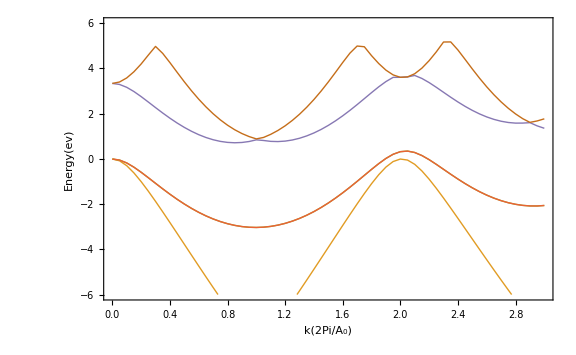

```mathematica
ListPlot[{silicondataset[[1]],silicondataset[[2]],silicondataset[[3]], silicondataset[[4]],silicondataset[[5]],silicondataset[[6]]},
Frame->True,Joined->{True},PlotMarkers->None,FrameLabel->{"k(2Pi/A_0)","Energy(ev)"},PlotRange->{-6,6}, LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},
PlotStyle->Thick,Background->White,ImageSize->Large]
```

```mathematica
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤5,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]
Length[generate0bases[5]]
```

137

### Comparing the band structure of Si and Ge along the direction <100> in the reciprocal lattice

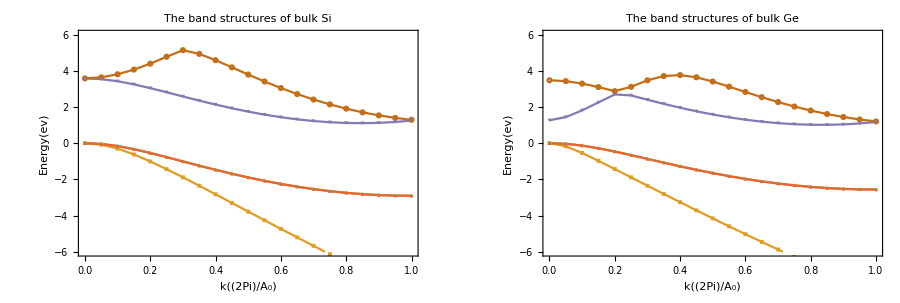

```mathematica
ClearAll["Global`*"]
NotebookSave[];

ry=13.6059;(*1 reydberg in eV*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)
Subscript[A, 0]={5.431020511,5.66};(*The lattice constant for Si and Ge, respectively in Angstroms*)

M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2); M[[2]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[2]])^2);

generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];
(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)

q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)

Subscript[k, x]=Range[0,1,0.05];
Kvec={1,0,0};
Subscript[V, f]={ry*{0, -0.113,0,0.02,0.04,0,0},{0, -1.57,0,0.07,0.41,0,0}};(*the list of the experimental form factors that will be used in the calculation of the hamiltonian
matrix elements*)

dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)



H[x__,y__,t__,element_]:=2 Subscript[V, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,2,If[√Abs[dot product[x-y,x-y]]==√8,4,
If[√Abs[dot product[x-y,x-y]]==√11,5,1]]]]] Cos[(Pi/4) dot product[y-x,t]];(*the hamiltonian matrix element, The term:(2*Subscript[V, f](q)*Cos(G-G').T)*)

h[x__,y__]:=(x+y).(x+y);(*the hamiltonian matrix element, The term:(|G+Kvec|^2 Subscript[δ, G',G])*)

HmatrixlistX1=Table[0,Length[Subscript[k, x]]];(*List of Hamiltonian matrices corresponding to different Subscript[k, x] value for Silicon*)
HmatrixlistX2=Table[0,Length[Subscript[k, x]]];(*List of Hamiltonian matrices corresponding to different Subscript[k, x] value for Germanium*)

eigenvaluesX1=Table[0,Length[Subscript[k, x]]];(*List of sets of eigenvalues, each set corresponds to different Subscript[k, x] value for Silicon*)
eigenvaluesX2=Table[0,Length[Subscript[k, x]]];(*List of sets of eigenvalues, each set corresponds to different Subscript[k, x] value for Germanium*)

Monitor[For[m=1,m<=Length[Subscript[k, x]],m++,Kvec[[1]]=Subscript[k, x][[m]];
HmatrixlistX1[[m]]=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],Kvec]+H[list[[j]],list[[i]],T,1],H[list[[j]],list[[i]],T,1]],
{j,1,Length[list]},{i,1,Length[list]}];HmatrixlistX2[[m]]=Table[If[list[[i]]==list[[j]],M[[2]]*h[list[[i]],Kvec]+H[list[[j]],list[[i]],T,2],H[list[[j]],list[[i]],T,2]],
{j,1,Length[list]},{i,1,Length[list]}];eigenvaluesX1[[m]]=Eigenvalues[HmatrixlistX1[[m]]];eigenvaluesX2[[m]]=Eigenvalues[HmatrixlistX2[[m]]]],
ProgressIndicator[m,{1,Length[Subscript[k, x]]}]];

(*Plotting*)               (*X stands for the direction <100>*)

silicondatasetX=Range[1,Length[list]];
GermaniumdatasetX=Range[1,Length[list]];

(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{Subscript[k, x][[i]],eigenvaluesX1[[i]][[Length[list]-1]]},{i,1,Length[Kvec]}];
shiftset2X=Table[{Subscript[k, x][[i]],eigenvaluesX2[[i]][[Length[list]-1]]},{i,1,Length[Kvec]}];
shift1X=Max[shiftset1X[[All,2]]];
shift2X=Max[shiftset2X[[All,2]]];

For[j=0,j<Length[list],j++,silicondatasetX[[j+1]]=Table[{Subscript[k, x][[i]],eigenvaluesX1[[i]][[Length[list]-j]]-shift1X},{i,1,Length[Subscript[k, x]]}];
GermaniumdatasetX[[j+1]]=Table[{Subscript[k, x][[i]],eigenvaluesX2[[i]][[Length[list]-j]]-shift2X},{i,1,Length[Subscript[k, x]]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)


GraphicsRow[{ListPlot[{silicondatasetX[[1]],silicondatasetX[[2]],silicondatasetX[[3]], silicondatasetX[[4]], silicondatasetX[[5]],silicondatasetX[[6]]},Frame->True,
Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-6,6},PlotMarkers->{Automatic, 4},PlotLabel->"The band structures of bulk Si"],ListPlot[{GermaniumdatasetX[[1]],
GermaniumdatasetX[[2]],GermaniumdatasetX[[3]], GermaniumdatasetX[[4]],GermaniumdatasetX[[5]],GermaniumdatasetX[[6]]},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},
PlotRange->{-6,6},PlotMarkers->{Automatic, 4},PlotLabel->"The band structures of bulk Ge"] },ImageSize->900]
```

```mathematica
GermaniumdatasetX[[5]]
```

{{0.,1.33223},{0.05,1.49916},{0.1,1.8663},{0.15,2.29713},{0.2,2.67645},{0.25,2.42848},{0.3,2.18261},{0.35,1.9467},{0.4,1.72574},{0.45,1.52301},{0.5,1.3408},{0.55,1.18075},{0.6,1.04413},{0.65,0.931959},{0.7,0.845086},{0.75,0.784265},{0.8,0.750182},{0.85,0.743473},{0.9,0.764736},{0.95,0.814532},{1.,0.893373}}

### Comparing the band structure of (Si) and (Ge) along the direction <111> in the reciprocal lattice

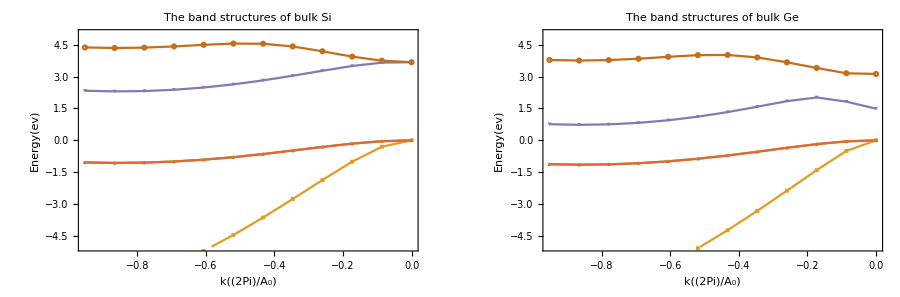

```mathematica
NotebookSave[];

Clear[Hmatrixlist1,Hmatrixlist2,eigenvalues1,eigenvalues2];
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000*{1.08,1};(*Effective masses for Si and Ge, respectively, in units of (Mev/c^2)*)
Subscript[A, 0]={5.43,5.66};(*The lattice constant for Si and Ge, respectively in Angstroms*)

M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0][[1]]*(Subscript[A, 0][[1]])^2); M[[2]]=(4.1357^2*9)/(2*Subscript[m, 0][[2]]*(Subscript[A, 0][[2]])^2);


generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];
(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)

Subscript[V, f]={ry*{0, -0.113,0,0.02,0.04,0,0},{0, -1.4,0,0.07,0.41,0,0}};
(*{{0, -1.43,0,0.27,0.54,0,0},{0, -1.57,0,0.07,0.41,0,0}};*)(*the list of the experimental form factors that will be used in the calculation of the hamiltonian
matrix elements*)
q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)

(*Setting up the direction and the equivalent vectors that have magnitude ≤ 1*)
kL=Range[-1,0,0.05];
Kvec=Table[kL[[i]]*{1,1,1},{i,1,Length[kL]}];
Kvec=DeleteCases[Kvec,n_/;dot product[n,n]>1];
Kvecmag=-Table[√(dot product[Kvec[[i]],Kvec[[i]]]),{i,1,Length[Kvec]}];


dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)

H[x__,y__,t__,element_]:=2 Subscript[V, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,2,If[√Abs[dot product[x-y,x-y]]==√8,4,
If[√Abs[dot product[x-y,x-y]]==√11,5,1]]]]] Cos[(Pi/4) dot product[y-x,t]];(*the hamiltonian matrix element, The term:(2*Subscript[V, f](q)*Cos(G-G').T)*)

h[x__,y__]:=(x+y).(x+y);(*the hamiltonian matrix element, The term:(|G+Kvec|^2 Subscript[δ, G',G])*)


Hmatrixlist1=Table[0,Length[Kvec]];(*List of Hamiltonian matrices corresponding to different Kvec value for Silicon*)
Hmatrixlist2=Table[0,Length[Kvec]];(*List of Hamiltonian matrices corresponding to different Kvec value for Germanium*)

eigenvalues1=Table[0,Length[Kvec]];(*List of sets of eigenvalues, each set corresponds to different Kvec value for Silicon*)
eigenvalues2=Table[0,Length[Kvec]];(*List of sets of eigenvalues, each set corresponds to different Kvec value for Germanium*)

Monitor[For[m=1,m≤Length[Kvec],m++,Hmatrixlist1[[m]]=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],Kvec[[m]]]+H[list[[j]],
list[[i]],T,1],H[list[[j]],list[[i]],T,1]],{j,1,Length[list]},{i,1,Length[list]}];Hmatrixlist2[[m]]=Table[If[list[[i]]==list[[j]],
M[[2]]*h[list[[i]],Kvec[[m]]]+H[list[[j]],list[[i]],T,2],H[list[[j]],list[[i]],T,2]],{j,1,Length[list]},{i,1,Length[list]}];
eigenvalues1[[m]]=Eigenvalues[Hmatrixlist1[[m]]];eigenvalues2[[m]]=Eigenvalues[Hmatrixlist2[[m]]]],ProgressIndicator[m,{1,Length[Kvec]}]];

(*Plotting*)

silicondatasetL=Range[1,Length[list]];
GermaniumdatasetL=Range[1,Length[list]];

(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1L=Table[{Kvecmag[[i]],eigenvalues1[[i]][[Length[list]-1]]},{i,1,Length[Kvecmag]}];
shiftset2L=Table[{Kvecmag[[i]],eigenvalues2[[i]][[Length[list]-1]]},{i,1,Length[Kvecmag]}];
shift1L=Max[shiftset1L[[All,2]]];
shift2L=Max[shiftset2L[[All,2]]];

For[j=0,j<Length[list],j++,silicondatasetL[[j+1]]=Table[{Kvecmag[[i]],eigenvalues1[[i]][[Length[list]-j]]-shift1L},{i,1,Length[Kvecmag]}];
GermaniumdatasetL[[j+1]]=Table[{Kvecmag[[i]],eigenvalues2[[i]][[Length[list]-j]]-shift2L},{i,1,Length[Kvecmag]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

GraphicsRow[{ListPlot[{silicondatasetL[[1]],silicondatasetL[[2]],silicondatasetL[[3]], silicondatasetL[[4]], silicondatasetL[[5]], 
silicondatasetL[[6]]},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-5,5},PlotMarkers->{Automatic, 4},
PlotLabel->"The band structures of bulk Si"],ListPlot[{GermaniumdatasetL[[1]],GermaniumdatasetL[[2]],GermaniumdatasetL[[3]], 
GermaniumdatasetL[[4]],GermaniumdatasetL[[5]],GermaniumdatasetL[[6]]},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},
PlotRange->{-5,5},PlotMarkers->{Automatic, 4},PlotLabel->"The band structures of bulk Ge"] },ImageSize->900]
```

### Standard form for displaying the band structure: Gathering data from both directions <100> & <111>

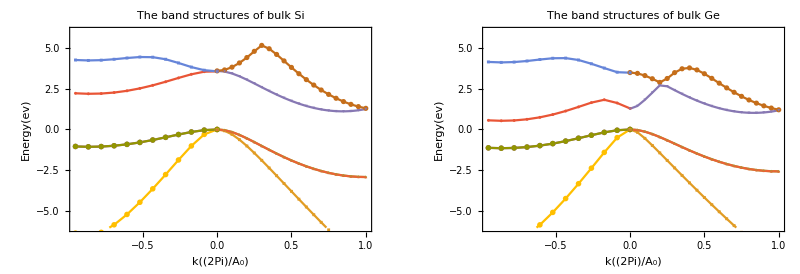

-Graphics-

```mathematica
silicondatasetL[[5]]=Table[{Kvecmag[[i]],eigenvalues1[[i]][[Length[list]-4]]-(shift1L+0.12)},{i,1,Length[Kvecmag]}];

silicondatasetL[[6]]=Table[{Kvecmag[[i]],eigenvalues1[[i]][[Length[list]-5]]-(shift1L+0.12)},{i,1,Length[Kvecmag]}];

GermaniumdatasetL[[5]]=Table[{Kvecmag[[i]],eigenvalues2[[i]][[Length[list]-4]]-(shift2L+0.2)},{i,1,Length[Kvecmag]}];

GermaniumdatasetL[[6]]=Table[{Kvecmag[[i]],eigenvalues2[[i]][[Length[list]-5]]-(shift2L-.35)},{i,1,Length[Kvecmag]}];

GraphicsRow[{ListPlot[{silicondatasetX[[1]],silicondatasetX[[2]],silicondatasetX[[3]], silicondatasetX[[4]], silicondatasetX[[5]],silicondatasetX[[6]],
silicondatasetL[[1]],silicondatasetL[[2]],silicondatasetL[[3]], silicondatasetL[[4]], silicondatasetL[[5]], silicondatasetL[[6]]},
Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-6,6},PlotMarkers->{Automatic, 3},
PlotLabel->"The band structures of bulk Si"],ListPlot[{GermaniumdatasetX[[1]],GermaniumdatasetX[[2]],GermaniumdatasetX[[3]], 
GermaniumdatasetX[[4]],GermaniumdatasetX[[5]],GermaniumdatasetX[[6]],GermaniumdatasetL[[1]],GermaniumdatasetL[[2]],GermaniumdatasetL[[3]], 
GermaniumdatasetL[[4]],GermaniumdatasetL[[5]],GermaniumdatasetL[[6]]},Frame->True,Joined->True,PlotMarkers->{Automatic, 3},FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},
PlotRange->{-6,6},PlotLabel->"The band structures of bulk Ge"] },ImageSize->800]

image=Import["Figure2.PNG"];
Image[image,Magnification->0.7]
```

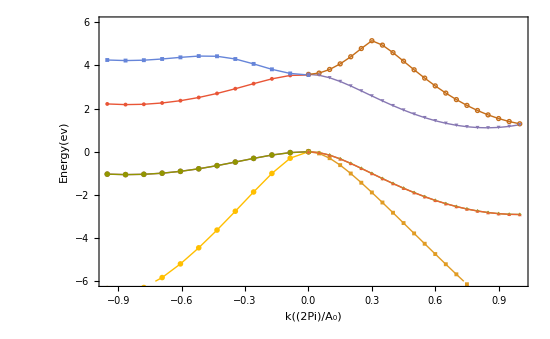

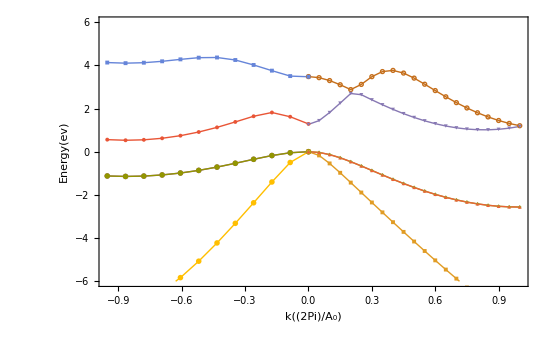

```mathematica
ListPlot[{silicondatasetX[[1]],silicondatasetX[[2]],silicondatasetX[[3]], silicondatasetX[[4]], silicondatasetX[[5]],silicondatasetX[[6]],
silicondatasetL[[1]],silicondatasetL[[2]],silicondatasetL[[3]], silicondatasetL[[4]], silicondatasetL[[5]], silicondatasetL[[6]]},
Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-6,6},PlotMarkers->{Automatic, 4},LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},PlotStyle->Thick,Background->White,ImageSize->550]

ListPlot[{GermaniumdatasetX[[1]],GermaniumdatasetX[[2]],GermaniumdatasetX[[3]], 
GermaniumdatasetX[[4]],GermaniumdatasetX[[5]],GermaniumdatasetX[[6]],GermaniumdatasetL[[1]],GermaniumdatasetL[[2]],GermaniumdatasetL[[3]], 
GermaniumdatasetL[[4]],GermaniumdatasetL[[5]],GermaniumdatasetL[[6]]},Frame->True,Joined->True,PlotMarkers->{Automatic, 4},FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},
PlotRange->{-6,6},LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black}, Background->White,PlotStyle->Thick,ImageSize->550]
```

```mathematica
silicondatasetX[[5]]
GermaniumdatasetX[[5]]
```

{{0.,3.58115},{0.05,3.54006},{0.1,3.42424},{0.15,3.25169},{0.2,3.04287},{0.25,2.81528},{0.3,2.5821},{0.35,2.35266},{0.4,2.13351},{0.45,1.92926},{0.5,1.74325},{0.55,1.57795},{0.6,1.43526},{0.65,1.31666},{0.7,1.22342},{0.75,1.15658},{0.8,1.11709},{0.85,1.10582},{0.9,1.12357},{0.95,1.17111},{1.,1.2492}}

{{0.,1.33223},{0.05,1.49916},{0.1,1.8663},{0.15,2.29713},{0.2,2.67645},{0.25,2.42848},{0.3,2.18261},{0.35,1.9467},{0.4,1.72574},{0.45,1.52301},{0.5,1.3408},{0.55,1.18075},{0.6,1.04413},{0.65,0.931959},{0.7,0.845086},{0.75,0.784265},{0.8,0.750182},{0.85,0.743473},{0.9,0.764736},{0.95,0.814532},{1.,0.893373}}

### The convergence of the band structure is mostly visible at the 65 plane-waves basis expansion

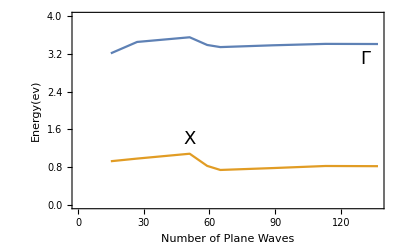

```mathematica
NotebookSave[];

num={15,27,51,59,65,89,113,137};

Subscript[E, Γ]={3.212,3.453,3.552,3.389,3.344,3.382,3.412,3.409};

Subscript[E, X]={0.926,0.982,1.085,0.827,0.741,0.781,0.825,0.821};

energydatasetΓ=Table[{num[[i]],Subscript[E, Γ][[i]]},{i,1,Length[Subscript[E, Γ]]}];

energydatasetX=Table[{num[[i]],Subscript[E, X][[i]]},{i,1,Length[Subscript[E, X]]}];

img9=ListPlot[{energydatasetΓ,energydatasetX},Joined->True,Frame->True,
FrameLabel->{"Number of Plane Waves","Energy(ev)"},LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},
PlotRange->{0,4},PlotLabels->Placed[{"Γ","X"},{Scaled[2],Above}]];

img10=Import["Table3.PNG"];
img11=Import["Figure4.PNG"];

GraphicsRow[{img9,img10,img11},ImageSize->1000]
```

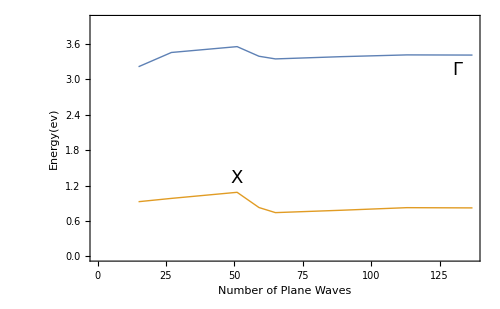

```mathematica
ListPlot[{energydatasetΓ,energydatasetX},Joined->True,Frame->True,
FrameLabel->{"Number of Plane Waves","Energy(ev)"},
PlotRange->{0,4},PlotLabels->Placed[{"Γ","X"},{Scaled[2],Above}],LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},PlotStyle->Thick,Background->White,ImageSize->500]
```

## Calculating the band structure of Compound Semiconductors: GaAs and InAs

A summary of Systematic Absences (Selection rules for miller indices):
Simple Cubic                                                                       All {h,k,l} are allowed
BCC                                                                                          h+k+l must be even
FCC                                                                                          {h,k,l} must be all odd or all even
*The structure of GaAs, AlAs, GaP,InP are all Zinc blend (FCC with basis)

### Along the direction <100> in the reciprocal lattice

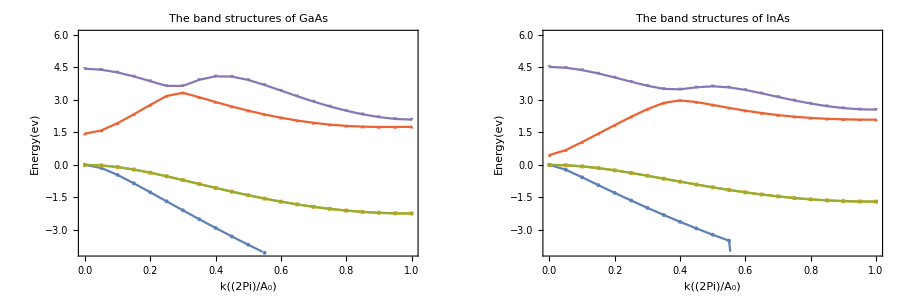

```mathematica
ClearAll["Global`*"]
NotebookSave[];

(*Symmetric and Asymmetric Form Factors for both GaAs and InAs*)
Subscript[symV, f]={{-3.13,0.00,0.14,0.82,0},{-2.99,0.00,0.00,0.68,0}};(*Symmetric Form Factors for GaAs and InAs,respectively *)
Subscript[asymV, f]={{0.95,0.68,0.00,0.14,0},{1.09,0.68,0.00,0.41,0}};(*Asymmetric Form Factors for GaAs and InAs,respectively*)

Subscript[A, 0]={5.65315,6.0583};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2); M[[2]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[2]])^2);

(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[4];


q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)
KvecX={1,0,0};(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kX=Range[0,1,0.05];

(*lists including 1 in their name correpond to GaAs and Those including 2 in their name correspond to InAs*)

HmatrixlistX1=Table[0,Length[kX]];(*List of Hamiltonian matrices corresponding to different kX value*)
HmatrixlistX2=Table[0,Length[kX]];(*List of Hamiltonian matrices corresponding to different kX value*)

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesX2=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)



dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)



H[x__,y__,t__,element_]:=Subscript[symV, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Cos[(Pi/4) dot product[y-x,t]] + I*Subscript[asymV, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Sin[(Pi/4) dot product[y-x,t]]
(*the hamiltonian matrix element, The term:(Subscript[V^S, f](q)*Cos(G-G').T+ⅈ*Subscript[V^A, f](q)*Sin(G-G').T)*)

h[x__,y__]:=dot product[x,x]+dot product[y,y]+2 dot product[x,y];
(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)

(*Producing the matrics*)
Monitor[For[m=1,m<=Length[kX],m++,KvecX[[1]]=kX[[m]];
HmatrixlistX1[[m]]=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],KvecX]+H[list[[j]],list[[i]],T,1],
H[list[[j]],list[[i]],T,1]],{j,1,Length[list]},{i,1,Length[list]}];HmatrixlistX2[[m]]=Table[If[list[[i]]==list[[j]],
M[[2]]*h[list[[i]],KvecX]+H[list[[j]],list[[i]],T,2],H[list[[j]],list[[i]],T,2]],{j,1,Length[list]},
{i,1,Length[list]}]],ProgressIndicator[m,{1,Length[kX]}]];                                 

(*Calculating the eigenvalues for each matrix*)
Monitor[For[i=1,i<=Length[kX],i++,eigenvaluesX1[[i]]=Eigenvalues[HmatrixlistX1[[i]]];
eigenvaluesX2[[i]]=Eigenvalues[HmatrixlistX2[[i]]]],ProgressIndicator[i,{1,Length[kX]}]];


(*Plotting*)               (*X stands for the direction <100>*)

dataset1X=Range[1,Length[list]];
dataset2X=Range[1,Length[list]];

(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shiftset2X=Table[{kX[[i]],eigenvaluesX2[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift2X=Max[shiftset2X[[All,2]]];

For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kX[[i]],eigenvaluesX1[[i]][[Length[list]-j]]-shift1X},{i,1,Length[kX]}];
dataset2X[[j+1]]=Table[{kX[[i]],eigenvaluesX2[[i]][[Length[list]-j]]-shift2X},{i,1,Length[kX]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)


GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],
dataset1X[[6]]},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-4,6},
PlotMarkers->{Automatic, 4},PlotLabel->"The band structures of GaAs"],ListPlot[{dataset2X[[2]],dataset2X[[3]], dataset2X[[4]],dataset2X[[5]],dataset2X[[6]]},Frame->True,
Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-4,6},PlotMarkers->{Automatic, 4},
PlotLabel->"The band structures of InAs"]},ImageSize->900]
```

### Along the direction <111> in the reciprocal lattice

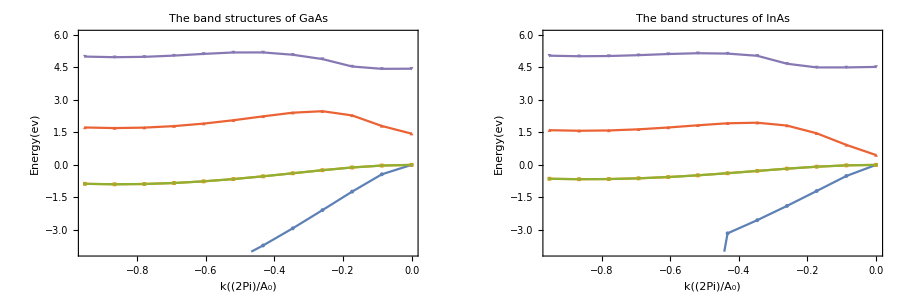

```mathematica
NotebookSave[];

(*Symmetric and Asymmetric Form Factors for both GaAs and InAs*)
Subscript[symV, f]={{-3.13,0.00,0.14,0.82,0},{-2.99,0.00,0.00,0.68,0}};(*Symmetric Form Factors for GaAs and InAs,respectively *)
Subscript[asymV, f]={{0.95,0.68,0.00,0.14,0},{1.09,0.68,0.00,0.41,0}};(*Asymmetric Form Factors for GaAs and InAs,respectively*)

Subscript[A, 0]={5.65315,6.0583};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2); M[[2]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[2]])^2);


list={{0,0,0},{1,1,1},{-1,1,1},{1,-1,1},{1,1,-1},{-1,-1,1},{1,-1,-1},{-1,1,-1},{-1,-1,-1},{2,0,0},{0,2,0},{0,0,2},{-2,0,0},
{0,-2,0},{0,0,-2},{2,2,0},{2,0,2},{0,2,2},{-2,2,0},{2,0,-2},{0,2,-2},{2,-2,0},{-2,0,2},{0,-2,2},{-2,-2,0},{-2,0,-2},{0,-2,-2},
{3,1,1},{1,3,1},{1,1,3},{-3,1,1},{-1,3,1},{-1,1,3},{3,-1,1},{1,-3,1},{1,-1,3},{1,1,-3},{3,1,-1},{1,3,-1},{-3,-1,1},{-1,-3,1},
{-1,-1,3},{3,-1,-1},{1,-3,-1},{1,-1,-3},{-3,1,-1},{-1,3,-1},{-1,1,-3},{-3,-1,-1},{-1,-3,-1},{-1,-1,-3},{2,2,2},{-2,2,2},
{2,-2,2},{2,2,-2},{-2,-2,2},{2,-2,-2},{-2,2,-2},{-2,-2,-2},{4,0,0},{0,4,0},{0,0,4},{-4,0,0},{0,-4,0},{0,0,-4}};
(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)

T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)


dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)


(*Setting up the direction and the equivalent vectors that have magnitude ≤ 1*)
klist=Range[-1,0,0.05];
kL=Table[klist[[i]]*{1,1,1},{i,1,Length[klist]}];
kL=DeleteCases[kL,n_/;dot product[n,n]>1];
kmag=-Table[√(dot product[kL[[i]],kL[[i]]]),{i,1,Length[kL]}];

(*lists including 1 in their names correpond to GaAs and Those including 2 in their names correspond to InAs*)

HmatrixlistL1=Table[0,Length[kL]];(*List of Hamiltonian matrices corresponding to different kL value*)
HmatrixlistL2=Table[0,Length[kL]];(*List of Hamiltonian matrices corresponding to different kL value*)

eigenvaluesL1=Table[0,Length[kL]];(*List of sets of eigenvalues, each set corresponds to different kL value*)
eigenvaluesL2=Table[0,Length[kL]];(*List of sets of eigenvalues, each set corresponds to different kL value*)



H[x__,y__,t__,element_]:=Subscript[symV, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Cos[(Pi/4) dot product[y-x,t]] + I*Subscript[asymV, f][[element]][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Sin[(Pi/4) dot product[y-x,t]]
(*the hamiltonian matrix element, The term:(Subscript[V^S, f](q)*Cos(G-G').T+ⅈ*Subscript[V^A, f](q)*Sin(G-G').T)*)

h[x__,y__]:=dot product[x,x]+dot product[y,y]+2 dot product[x,y];
(*the hamiltonian matrix element, The term:(|G+k|^2 Subscript[δ, G',G])*)

(*Producing the matrics*)
Monitor[For[m=1,m<=Length[kL],m++,HmatrixlistL1[[m]]=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],kL[[m]]]+H[list[[j]],list[[i]],T,1],
H[list[[j]],list[[i]],T,1]],{j,1,Length[list]},{i,1,Length[list]}];HmatrixlistL2[[m]]=Table[If[list[[i]]==list[[j]],
M[[2]]*h[list[[i]],kL[[m]]]+H[list[[j]],list[[i]],T,2],H[list[[j]],list[[i]],T,2]],{j,1,Length[list]},
{i,1,Length[list]}]],ProgressIndicator[m,{1,Length[kL]}]];                                 


(*Calculating the eigenvalues for each matrix*)
Monitor[For[i=1,i<=Length[kL],i++,eigenvaluesL1[[i]]=Eigenvalues[HmatrixlistL1[[i]]];
eigenvaluesL2[[i]]=Eigenvalues[HmatrixlistL2[[i]]]],ProgressIndicator[i,{1,Length[kL]}]];

(*Plotting*)               (*L stands for the direction <111>*)

dataset1L=Range[1,Length[list]]; (*Each dataset will correspond to an eigenstate with eigenvalue that is a function in k*)
dataset2L=Range[1,Length[list]]; (*Therefore, the number of datasets equals the number of eigenstates = Length[list]*)

(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1L=Table[{kmag[[i]],eigenvaluesL1[[i]][[Length[list]-1]]},{i,1,Length[kmag]}];
shiftset2L=Table[{kmag[[i]],eigenvaluesL2[[i]][[Length[list]-1]]},{i,1,Length[kmag]}];
shift1L=Max[shiftset1L[[All,2]]];
shift2L=Max[shiftset2L[[All,2]]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{kmag[[i]],eigenvaluesL1[[i]][[Length[list]-j]]-shift1L},
{i,1,Length[kL]}];dataset2L[[j+1]]=Table[{kmag[[i]],eigenvaluesL2[[i]][[Length[list]-j]]-shift2L},{i,1,Length[kL]}]];
(*each eigenvalues list of eigenvalues1 starts with largest eigenvalue so, I reverse the index j >>>> Length[list]-j*)


GraphicsRow[{ListPlot[{dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],
dataset1L[[6]]},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-4,6},
PlotMarkers->{Automatic, 4},PlotLabel->"The band structures of GaAs"],ListPlot[{
dataset2L[[2]],dataset2L[[3]], dataset2L[[4]],dataset2L[[5]],dataset2L[[6]]},Frame->True,
Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-4,6},PlotMarkers->{Automatic, 4},
PlotLabel->"The band structures of InAs"]},ImageSize->900]
```

### The standard form of band structure for GaAs and InAs

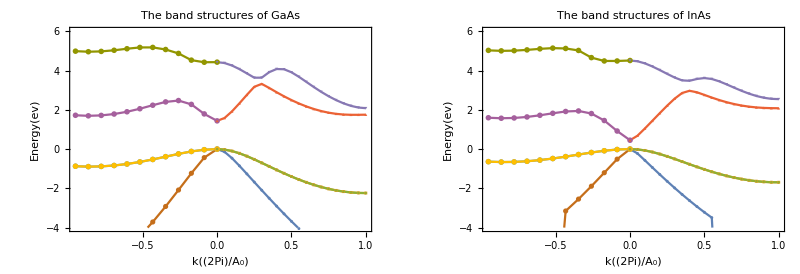

-Graphics-

```mathematica
GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],
dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]], dataset1L[[6]]},
Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-4,6},PlotMarkers->{Automatic, 3},
PlotLabel->"The band structures of GaAs"],ListPlot[{dataset2X[[2]],dataset2X[[3]], 
dataset2X[[4]],dataset2X[[5]],dataset2X[[6]],dataset2L[[2]],dataset2L[[3]], 
dataset2L[[4]],dataset2L[[5]],dataset2L[[6]]},Frame->True,Joined->True,PlotMarkers->{Automatic, 3},FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},
PlotRange->{-4,6},PlotLabel->"The band structures of InAs"] },ImageSize->800]

image=Import["Figure6.PNG"];
Image[image,Magnification->0.8]
```

```mathematica
dataset2L[[5]]
dataset2X[[5]]
```

{{-0.952628,1.59762},{-0.866025,1.57165},{-0.779423,1.58578},{-0.69282,1.63786},{-0.606218,1.72173},{-0.519615,1.824},{-0.433013,1.91657},{-0.34641,1.94274},{-0.259808,1.8112},{-0.173205,1.45545},{-0.0866025,0.920488},{0.,0.451977}}

{{0.,0.451977},{0.05,0.680628},{0.1,1.05046},{0.15,1.43992},{0.2,1.83123},{0.25,2.21319},{0.3,2.56848},{0.35,2.8559},{0.4,2.97082},{0.45,2.89422},{0.5,2.76066},{0.55,2.62406},{0.6,2.4981},{0.65,2.38748},{0.7,2.29423},{0.75,2.21917},{0.8,2.16226},{0.85,2.12251},{0.9,2.09785},{0.95,2.08511},{1.,2.08112}}

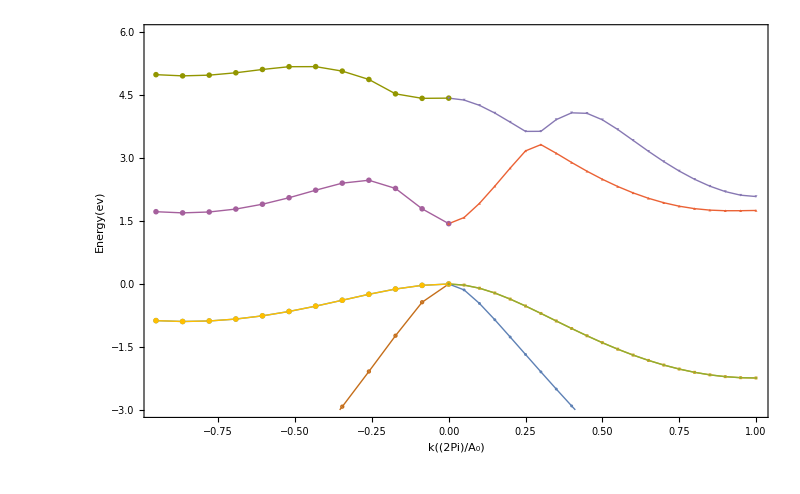

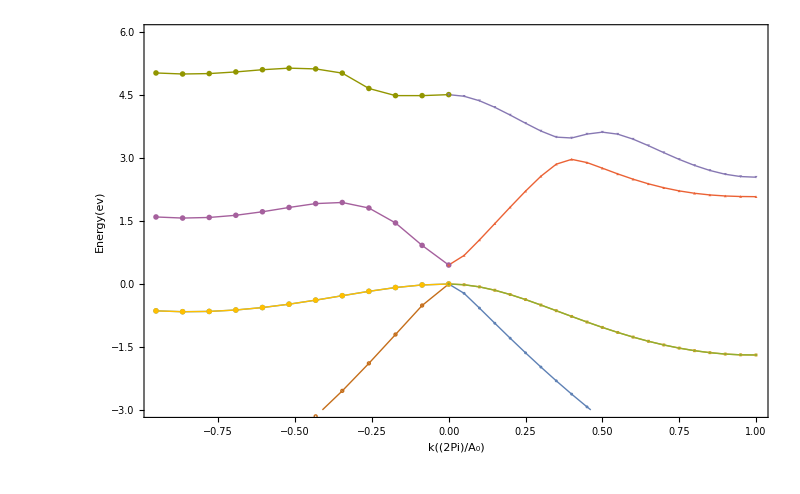

```mathematica
ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],
dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]], dataset1L[[6]]},
Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-3,6},LabelStyle -> {FontFamily -> "Arial", FontSize -> 20, Black},
PlotMarkers->{Automatic, 3},Background->White,Background->White,PlotStyle->Thick]

ListPlot[{dataset2X[[2]],dataset2X[[3]], 
dataset2X[[4]],dataset2X[[5]],dataset2X[[6]],dataset2L[[2]],dataset2L[[3]], 
dataset2L[[4]],dataset2L[[5]],dataset2L[[6]]},
Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},PlotRange->{-3,6},LabelStyle -> {FontFamily -> "Arial", FontSize -> 20, Black},
PlotMarkers->{Automatic, 3},Background->White,PlotStyle->Thick]
```

## Calculating the charge density for Si and GaAs

I will calculate the charge density by two different ways, The first one is by brute force by summing the probability density over all values of “k” in the first Brillouin zone. The second one is by exploiting the symmetry of the silicon crystal to find a “Mean-value point”. At this point, the value that a given periodic function takes, will be a very good approximation to the average value of the function over all k.
*I will talk more about the theory of the second method in my thesis, since it is more computationally economic than the brute force method and can be used for calculating other crystal optical properties.

### Brute force calculation (Silicon case) by summing over all K along <100>

```mathematica
ClearAll["Global`*"];
NotebookSave[];

hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)
A={5.431020511};(*The lattice constant for Si and Ge, respectively in Angstroms*)

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=N[(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2),5];
(*The atomic form factors of GaP*)
Vform0list={-1.43,0,0.27,0.54};

(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

form0factor[m_]:=Vform0list[[1]]/;m==3
form0factor[m_]:=Vform0list[[2]]/;m==4
form0factor[m_]:=Vform0list[[3]]/;m==8
form0factor[m_]:=Vform0list[[4]]/;m==11
form0factor[m_]:=0

V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec]],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+row0qvec).(kvec+row0qvec))*If[row0qvec==col0qvec,1,0];

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];

list=generate0bases[6];
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{1,1,1},{-1,-1,-1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.05];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
kX0length=Length[kX];

(*Calculations*)
Hmatrix;
eigenvalues;
mat0eigenvectors={};
num0valence0bands=4;

(*First, Finding the first four eigenvectors corresponding to the first four valence bands*)
Monitor[
Do[
Hmatrix=Table[N[Re[mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist]],8],{i,1,list0length},{j,1,list0length}];
eigenvalues = N[Re[Eigenvalues[Hmatrix]],8];
Do[mat0eigenvectors=Append[mat0eigenvectors,First@NullSpace[Hmatrix - eigenvalues[[-k]]*IdentityMatrix[list0length]]]
,{k,1,num0valence0bands}];
Clear[Hmatrix,eigenvalues]
,{m,1,kX0length}],ProgressIndicator[m,{1,kX0length}]]

(*Calculating the charge density by summing over the four valence bands and all k values*)
zplanes=Table[0.125*i,{i,0,4}];
coordinate0list=Flatten[Table[{i,j},{i,0,1,0.01},{j,0,1,0.01}],1];
exp0vec0pos[point_]:=Table[Exp[2 Pi I (list[[i]].point)],{i,1,list0length}];

density0pos[exp0vec0pos,point_,zplane_,mat_]:=density0pos[exp0vec0pos,point,zplane,mat]=Module[{eigenvectors,exp0vec},
exp0vec=exp0vec0pos[{point[[2]],point[[1]],zplane}];
eigenvectors=mat.exp0vec;
Return[eigenvectors.Conjugate[eigenvectors]]
]

dataset[density0pos,zplane_,mat_]:=
Table[{coordinate0list[[i]][[2]],coordinate0list[[i]][[1]],Re[density0pos[exp0vec0pos,coordinate0list[[i]],zplane,mat]]},
{i,1,Length[coordinate0list]}];
```

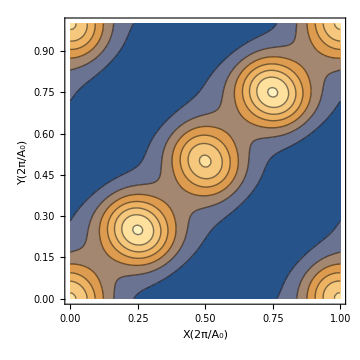

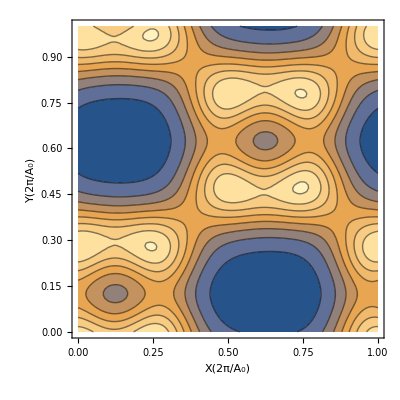

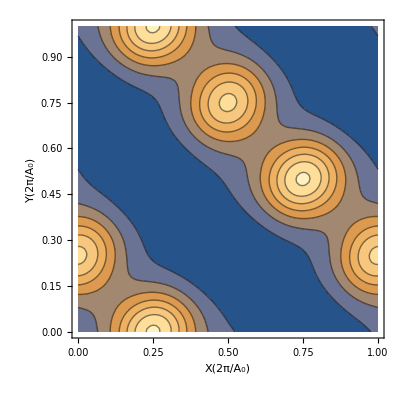

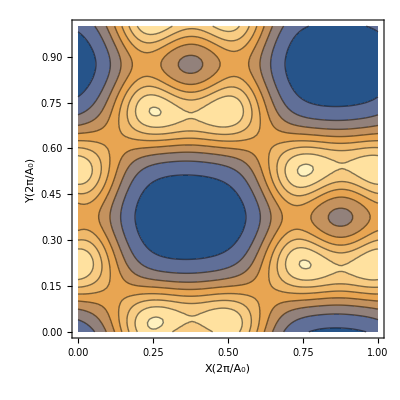

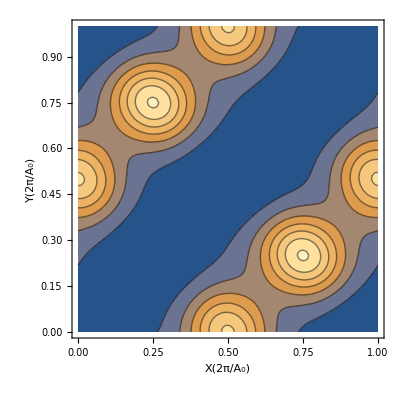

```mathematica
Do[Print[ListContourPlot[dataset[density0pos,zplanes[[i]],mat0eigenvectors],FrameLabel->{"X(2π/A_0)","Y(2π/A_0)"},LabelStyle -> {FontFamily -> "Arial", FontSize -> 15, Black}]],{i,1,Length[zplanes]}]
```

#### Parallelized code for the brute force calculation:

```mathematica
(*This function is for displaying the progress bar for the buit-in function "ParallelMap". It doesn't relate to the code itself and can 
be removed with replaceing the function"monitorParallelMap" name by the built-in function "ParallelMap"*)
(*ClearAll[monitorParallelMap];
monitorParallelMap[foo_, expr_, levelSpec_: {1}, 
  opts : OptionsPattern[ParallelMap]] :=
 Module[{res, exprCount, progress = 0},
  SetSharedVariable[progress];
  exprCount = Length@Level[expr, levelSpec];
  res =
   Monitor[
    ParallelMap[(Pause[.25]; progress++; foo[#]) &, expr, levelSpec, opts],
    Column[{ToString@progress <> " of " <> ToString@exprCount, 
      ProgressIndicator[progress, {0, exprCount}]}, 
     Alignment -> Center]
    ];
  UnsetShared [progress];
  res
  ]*)

(*

(*The 5 planes that the charge density will be calculated in, defined by their z values*)
zplanes=Range[0.00,0.50,0.125];
(*The coordinate system is cartesian for fcc lattice of Silicon*)
xyplane=Range[Length[zplanes]];
For[k=1,k≤Length[zplanes],k++,xyplane[[k]]=Flatten[Table[{i,j,zplanes[[k]]},{j,0,1,0.01},{i,0,1,0.01}],1]]

(*This function is very important since I have noticed that the list of eigenvectors produced by mathematica for a certain matrix do not 
necessarily correspond to the order of the eigenvalues for the same matrix. Therefore, I needed to make sure that I am summing over the 
4 valence eigenstates not any other states.*)
eigenVector98[n_,i_]:=First@NullSpace[Hmatrixlist[[n]] - eigenvalues[[n]][[i]] IdentityMatrix[65]]


num0valence0bands=4;

density[pos_]:=density[pos]=Module[{vec1,vec0total},
Clear[vec0total];
vec0total=Range[Length[zplanes]];

Do[
Do[
vec1=eigenVector98[c,v];
Do[vec1[[i]]=vec1[[i]]*Exp[2*Pi*I*list[[i]].xyplane[[z]][[pos]]],{i,1,Length[vec1]}];
vec0total[[z]]=vec0total[[z]]+Re[Conjugate[Total[vec1]]*Total[vec1]];
,{c,1,Length[Subscript[k, x]]},{v,62,65}],
{z,1,Length[zplanes]}];
Return[vec0total]
]

all0density=ParallelMap[density,Range[1,Length[xyplane[[1]]]]];

Do[
Do[
xyplane[[i]][[j]][[3]]=all0density[[j]][[i]],
{j,1,Length[xyplane[[1]]]}
],
{i,1,Length[zplanes]}
]

Do[Print[ListContourPlot[xyplane[[i]]]],{i,Length[zplanes]}]*)
```

### Mean-Value Point Technique (Silicon case)

```mathematica
ClearAll["Global`*"];
NotebookSave[];

hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)
Subscript[A, 0]={5.431020511,5.66};(*The lattice constant for Si and Ge, respectively in Angstroms*)

M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2); M[[2]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[2]])^2);


Subscript[V, f]={{0, -1.43,0,0.27,0.54,0,0},{0, -1.57,0,0.07,0.41,0,0}};(*the list of the experimental form factors that will be used in the calculation of the hamiltonian
matrix elements*)

T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)



H[x__,y__,t__,element_]:=2 Subscript[V, f][[element]][[If[√Abs[(x-y).(x-y)]==√3,2,If[√Abs[(x-y).(x-y)]==√8,4,
If[√Abs[(x-y).(x-y)]==√11,5,1]]]]] Cos[(Pi/4) (y-x).t];(*the hamiltonian matrix element, The term:(2*Subscript[V, f](q)*Cos(G-G').T)*)

h[x__,y__]:=(x+y).(x+y);(*the hamiltonian matrix element, The term:(|G+Kvec|^2 Subscript[δ, G',G])*)



(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];




kvector={0.6223,0.2953,0};

Hmatrixlist7=Monitor[Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],kvector]+H[list[[j]],list[[i]],T,1],H[list[[j]],list[[i]],T,1]],
{j,1,Length[list]},{i,1,Length[list]}],ProgressIndicator[i,1,{1,Length[list]}]];


eigenvectors7=Eigenvectors[Hmatrixlist7];

(*The 5 planes that the charge density will be calculated in, defined by their z values*)
zplanes=Range[0.00,0.50,0.125];
(*The coordinate system is cartesian for fcc lattice of Silicon*)
xyplane=Range[Length[zplanes]];
For[k=1,k≤Length[zplanes],k++,xyplane[[k]]=Table[{i,j,zplanes[[k]]},{j,0,1,0.01},{i,0,1,0.01}]]



num0valence0bands=4;

charge0density0plane=Range[Length[zplanes]];

Do[charge0density0plane[[i]]=Table[0,{m,Dimensions[xyplane[[i]]][[1]]},{n,Dimensions[xyplane[[i]]][[2]]}],{i,Length[zplanes]}]

(*Equation 15.9 for the wavefunction as a linear combination of the complete orthogonal basis set "Ψ_(n, k)=Σ_Ga_(n, k)e^(i(G + k) . r)"*)
(*Calculating the charge density by calculating the probability density "ρ = ((Ψ_(n, k))^*)*(Ψ_(n, k))"*)
density[matrices_,pos_]:=density[matrices,pos]=Re[Sum[matrices[[Length[list]-n]][[G']]*matrices[[Length[list]-n]][[G]]
*Exp[2*Pi*I*((list[[G]]-list[[G']]).pos)],{n,0,num0valence0bands-1},
{G,1,Length[list]},{G',1,Length[list]}]];

Monitor[For[i=1,i≤Length[zplanes],i++,Do[charge0density0plane[[i]][[x1]][[y1]]={xyplane[[i]][[x1]][[y1]][[1]],
xyplane[[i]][[x1]][[y1]][[2]],density[eigenvectors7,xyplane[[i]][[x1]][[y1]]]},
{x1,Dimensions[xyplane[[1]]][[1]]},{y1,Dimensions[xyplane[[1]]][[1]]}]],ProgressIndicator[i,{1,Length[zplanes]}]]
```

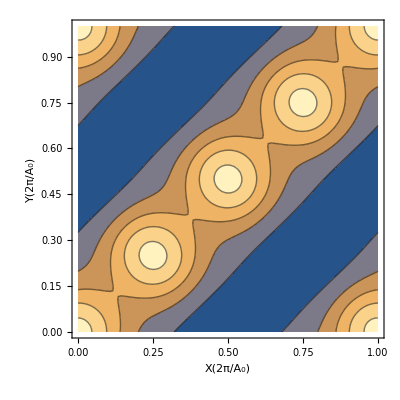

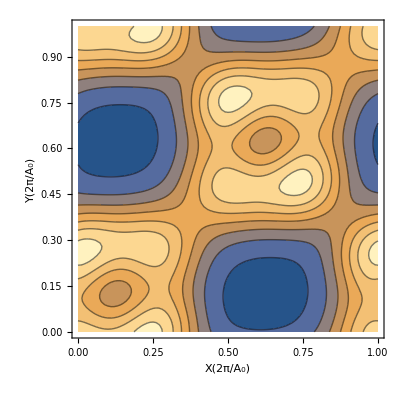

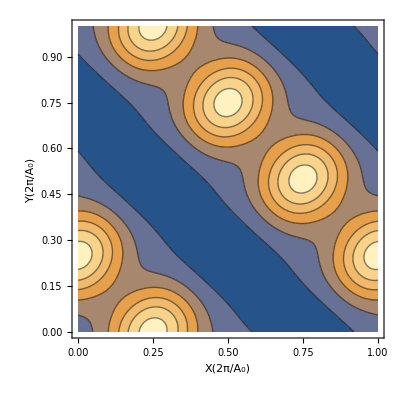

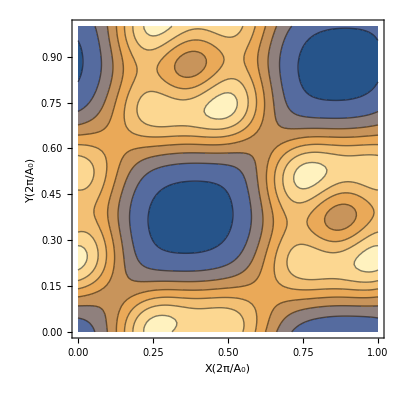

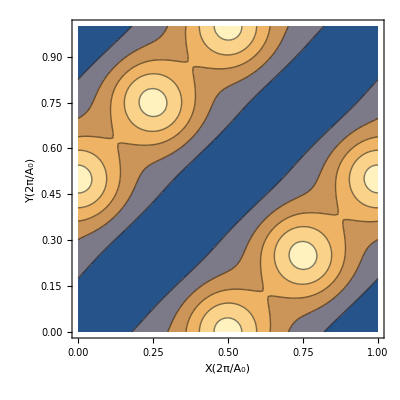

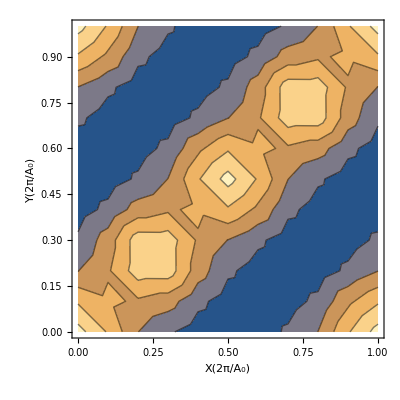

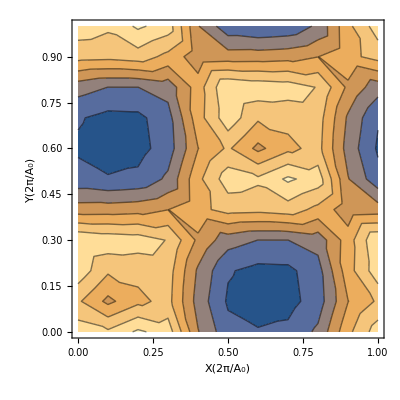

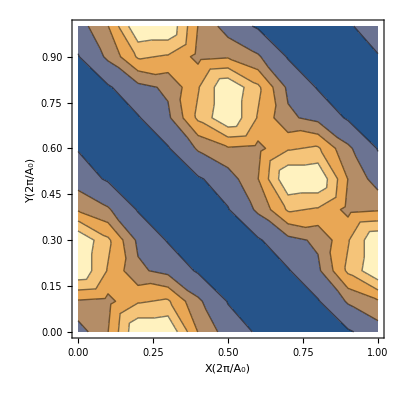

```mathematica
Do[Print[ListContourPlot[Flatten[charge0density0plane[[i]],1],FrameLabel->{"X(2π/A_0)","Y(2π/A_0)"},LabelStyle -> {FontFamily -> "Arial", FontSize -> 15, Black}
]],{i,Length[zplanes]}]
```

### Brute force calculation (GaAs case) by summing over all K along <100>

```mathematica
ClearAll["Global`*"]
NotebookSave[];

(*Symmetric and Asymmetric Form Factors for GaAs*)
symV={-3.13,0.00,0.14,0.82,0};(*Symmetric Form Factors for GaAs*)
asymV={0.95,0.68,0.00,0.14,0};(*Asymmetric Form Factors for GaAs*)

Subscript[A, 0]={5.65315};(*Lattice constant for GaAs in Angstroms*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=4.71302970190837(*N[(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2),5]*);


(*These functions are just definitions to generalize the code for different materials with different form factors*)
form0factor[m_,bases0index_]:=symV[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=symV[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=symV[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=symV[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=asymV[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=asymV[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=asymV[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=asymV[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]



V[form0factor,qvec_,baseslist_]:=Module[{},
Return[form0factor[Abs[qvec.qvec],1]*Cos[Pi/4 (qvec.baseslist[[1]])]+
I*form0factor[Abs[qvec.qvec],2]*Sin[Pi/4 (qvec.baseslist[[1]])]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+row0qvec).(kvec+row0qvec))*If[row0qvec==col0qvec,1,0];

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=
h[row0qvec,col0qvec,kvec]+V[form0factor,col0qvec-row0qvec,baseslist];

list=generate0bases[6];
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{1,1,1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.05];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
kX0length=Length[kX];

(*Calculations*)
Hmatrix;
eigenvalues;
mat0eigenvectors={};
num0valence0bands=4;

(*First, Finding the first four eigenvectors corresponding to the first four valence bands*)
Monitor[
Do[
Hmatrix=Table[mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist],{i,1,list0length},{j,1,list0length}];
eigenvalues = N[Re[Eigenvalues[Hmatrix]],8];
Do[mat0eigenvectors=Append[mat0eigenvectors,First@NullSpace[Hmatrix - eigenvalues[[-k]]*IdentityMatrix[list0length]]]
,{k,1,num0valence0bands}];
Clear[Hmatrix,eigenvalues]
,{m,1,kX0length}],ProgressIndicator[m,{1,kX0length}]]


(*Calculating the charge density by summing over the four valence bands and all k values*)
zplanes=Table[0.125*i,{i,0,4}];
coordinate0list=Flatten[Table[{i,j},{i,0,1,0.01},{j,0,1,0.01}],1];
exp0vec0pos[point_]:=Table[Exp[2 Pi I (list[[i]].point)],{i,1,list0length}];

density0pos[exp0vec0pos,point_,zplane_,mat_]:=density0pos[exp0vec0pos,point,zplane,mat]=Module[{eigenvectors,exp0vec},
exp0vec=exp0vec0pos[{point[[2]],point[[1]],zplane}];
eigenvectors=mat.exp0vec;
Return[eigenvectors.Conjugate[eigenvectors]]
]

dataset[density0pos,zplane_,mat_]:=
Table[{coordinate0list[[i]][[2]],coordinate0list[[i]][[1]],Re[density0pos[exp0vec0pos,coordinate0list[[i]],zplane,mat]]},
{i,1,Length[coordinate0list]}];
```

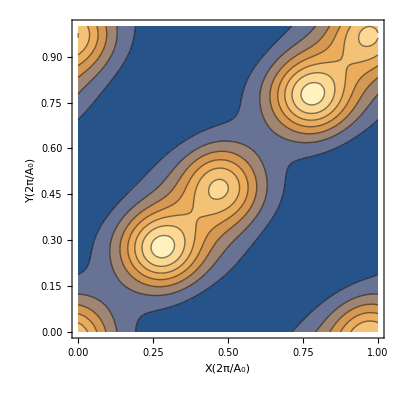

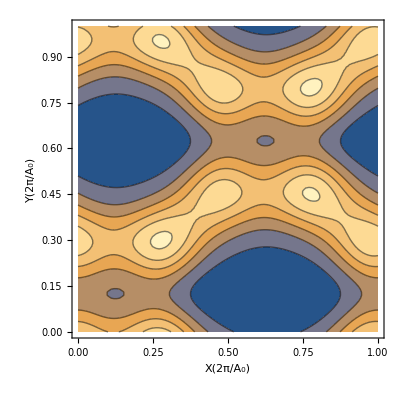

-Graphics-

-Graphics-

-Graphics-

```mathematica
Do[Print[ListContourPlot[dataset[density0pos,zplanes[[i]],mat0eigenvectors],FrameLabel->{"X(2π/A_0)","Y(2π/A_0)"},LabelStyle -> {FontFamily -> "Arial", FontSize -> 15, Black}
]],{i,1,Length[zplanes]}]
```

#### Parallelized Code for the brute force calculation:

```mathematica
mat={}; 
xyplane1=Range[Length[zplanes]];
Do[xyplane1[[k]]=Flatten[Table[{i,j,zplanes[[k]]},{i,0,1,0.1},{j,0,1,0.1}],1],{k,1,Length[zplanes]}]
contour0list=Range[zplanes];

eigenVector99[n_,i_] := 
 First@NullSpace[Hmatrixlist[[n]] - eigenvalues[[n]][[i]] IdentityMatrix[65]]

Do[mat=Append[mat,eigenVector99[m1,m2]],
{m1,Length[kX]},{m2,Length[list]-3,Length[list]}];
mat=Transpose[mat];

efactor[x_]:=Module[{mat1},
Clear[mat1];
mat1=Range[1,Length[zplanes]];
Do[mat1[[m]]=Table[0,{i,1,Dimensions[mat][[1]]},{j,1,Dimensions[mat][[2]]}],{m,1,Length[zplanes]}];

Do[
For[
i=1,i≤Length[list],i++,
For[
v=1,v≤Dimensions[mat][[2]],v++,
mat1[[k]][[i]][[v]]=mat[[i]][[v]]*Exp[2*Pi*I*dot product[list[[i]],xyplane1[[k]][[x]]]]
]
],
{k,1,Length[zplanes]}
];

Return[mat1]]

f3[x_]:=ParallelMap[efactor,Range[1,x]]


list0mat=f3[Length[xyplane1[[1]]]];
zlist=Range[Length[zplanes]];
For[n=1,n≤Length[zplanes],n++,
For[i=1,i≤Length[list0mat],i++,

zlist[[n]]=Total[list0mat[[i]][[n]]];

xyplane1[[n]][[i]][[3]]=Sum[Re[Conjugate[zlist[[n]][[k]]]*zlist[[n]][[k]]],
{k,1,Dimensions[mat][[2]]}]]]

Do[Print[ListContourPlot[xyplane1[[i]]]],{i,1,Length[zplanes]}]
```

### Mean-Value point Technique (GaAs case)

```mathematica
ClearAll["Global`*"]
NotebookSave[];

(*Symmetric and Asymmetric Form Factors for GaAs*)
Subscript[symV, f]={-3.13,0.00,0.14,0.82,0};(*Symmetric Form Factors for GaAs*)
Subscript[asymV, f]={0.95,0.68,0.00,0.14,0};(*Asymmetric Form Factors for GaAs*)

Subscript[A, 0]={5.65315};(*Lattice constant for GaAs in Angstroms*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=4.71302970190837(*N[(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2),5]*);


list={{0,0,0},{1,1,1},{-1,1,1},{1,-1,1},{1,1,-1},{-1,-1,1},{1,-1,-1},{-1,1,-1},{-1,-1,-1},{2,0,0},{0,2,0},{0,0,2},{-2,0,0},
{0,-2,0},{0,0,-2},{2,2,0},{2,0,2},{0,2,2},{-2,2,0},{2,0,-2},{0,2,-2},{2,-2,0},{-2,0,2},{0,-2,2},{-2,-2,0},{-2,0,-2},{0,-2,-2},
{3,1,1},{1,3,1},{1,1,3},{-3,1,1},{-1,3,1},{-1,1,3},{3,-1,1},{1,-3,1},{1,-1,3},{1,1,-3},{3,1,-1},{1,3,-1},{-3,-1,1},{-1,-3,1},
{-1,-1,3},{3,-1,-1},{1,-3,-1},{1,-1,-3},{-3,1,-1},{-1,3,-1},{-1,1,-3},{-3,-1,-1},{-1,-3,-1},{-1,-1,-3},{2,2,2},{-2,2,2},
{2,-2,2},{2,2,-2},{-2,-2,2},{2,-2,-2},{-2,2,-2},{-2,-2,-2},{4,0,0},{0,4,0},{0,0,4},{-4,0,0},{0,-4,0},{0,0,-4}};
(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)


q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)
KvecX={1,0,0};(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kX=Range[0,1,0.1];

(*The 5 planes that the charge density will be calculated in, defined by their z values*)
zplanes=Range[0.00,0.50,0.125];

num0valence0bands=4;

(*lists including 1 in their name correpond to GaAs and Those including 2 in their name correspond to InAs*)

Hmatrixlist=Table[0,Length[kX]];(*List of Hamiltonian matrices corresponding to different kX value*)

eigenvectors=Table[0,Length[kX]];(*List of sets of eigenvectors, each set corresponds to different kX value*)
eigenvalues=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)

dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)

(*the hamiltonian matrix element, The term:(Subscript[V^S, f](q)*Cos(G-G').T+ⅈ*Subscript[V^A, f](q)*Sin(G-G').T)*)
H[x__,y__,t__]:=Subscript[symV, f][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Cos[(Pi/4) dot product[y-x,t]] + I*Subscript[asymV, f][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Sin[(Pi/4) dot product[y-x,t]]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[x__,y__]:=dot product[x,x]+dot product[y,y]+2 dot product[x,y];


(*Producing the matrics*)
Monitor[For[m=1,m<=Length[kX],m++,KvecX[[1]]=kX[[m]];Hmatrixlist[[m]]=Table[If[list[[i]]==list[[j]],
M[[1]]*h[list[[i]],KvecX]+H[list[[j]],list[[i]],T],H[list[[j]],list[[i]],T]],{j,1,Length[list]},
{i,1,Length[list]}]],ProgressIndicator[m,{1,Length[kX]}]];                                 

(*Calculating the eigenvectors for each matrix*)
Monitor[For[i=1,i≤Length[kX],i++,eigenvectors[[i]]=Eigenvectors[Hmatrixlist[[i]]];eigenvalues[[i]]=Eigenvalues[Hmatrixlist[[i]]]],
ProgressIndicator[i,{1,Length[kX]}]];

kvector={0.25,0.25,0.25}; 
(*This is the value for the value-point for a zinc blende cubic structure obtained from Baldcreschi's paper, 1972*)

Hmatrixlist7=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],kvector]+H[list[[j]],list[[i]],T],H[list[[j]],list[[i]],T]],
{j,1,Length[list]},{i,1,Length[list]}];
(*I will try to find the set of eigenvectors and eigenvalues for this value of k point by constructing 
the hamiltonian matrix just like before*)


eigenvectors7=Eigenvectors[Hmatrixlist7];

(*The 5 planes that the charge density will be calculated in, defined by their z values*)
zplanes=Range[0.00,0.50,0.125];
(*The coordinate system is cartesian for fcc lattice of Silicon*)
xyplane=Range[Length[zplanes]];
For[k=1,k≤Length[zplanes],k++,xyplane[[k]]=Table[{i,j,zplanes[[k]]},{j,0,1,0.01},{i,0,1,0.01}]]

charge0density0plane=Range[Length[zplanes]];

Do[charge0density0plane[[i]]=Table[0,{m,Dimensions[xyplane[[i]]][[1]]},{n,Dimensions[xyplane[[i]]][[2]]}],{i,Length[zplanes]}]

(*Equation 15.9 for the wavefunction as a linear combination of the complete orthogonal basis set "Ψ_(n, k)=Σ_Ga_(n, k)e^(i(G + k) . r)"*)
(*Calculating the charge density by calculating the probability density "ρ = ((Ψ_(n, k))^*)*(Ψ_(n, k))"*)
(*density[matrices_,pos_]:=density[matrices,pos]=Re[Sum[Conjugate[matrices[[Length[list]-n]][[G']]]*matrices[[Length[list]-n]][[G]]
*Exp[2*Pi*I*dot product[list[[G']]-list[[G]],pos]],{n,0,num0valence0bands-1},
{G,1,Length[list]},{G',1,Length[list]}]];*)

density1[matrices_,pos_]:=density1[matrices,pos]=Re[Sum[Conjugate[matrices[[Length[list]-n]][[G']]]*matrices[[Length[list]-n]][[G]]
*Exp[2*Pi*I*dot product[list[[G']]-list[[G]],pos]],{n,0,num0valence0bands-1},
{G,1,Length[list]},{G',1,Length[list]}]];

Monitor[For[i=1,i≤Length[zplanes],i++,Do[charge0density0plane[[i]][[x1]][[y1]]={xyplane[[i]][[x1]][[y1]][[1]],
xyplane[[i]][[x1]][[y1]][[2]],density1[eigenvectors7,xyplane[[i]][[x1]][[y1]]]},
{x1,Dimensions[xyplane[[1]]][[1]]},{y1,Dimensions[xyplane[[1]]][[1]]}]],ProgressIndicator[i,{1,Length[zplanes]}]]
```

```mathematica
Do[Print[ListContourPlot[Flatten[charge0density0plane[[i]],1],FrameLabel->{"X(2π/A_0)","Y(2π/A_0)"},LabelStyle -> {FontFamily -> "Arial", FontSize -> 15, Black}]],{i,Length[zplanes]}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

## Calculating effective mass (m*) of the lowest energy band of GaAs at Γ point

### Calculating Eigenvalues as before

```mathematica
ClearAll["Global`*"]
NotebookSave[];

(*Symmetric and Asymmetric Form Factors for GaAs*)
Subscript[symV, f]={-3.13,0.00,0.14,0.82,0};(*Symmetric Form Factors for GaAs*)
Subscript[asymV, f]={0.95,0.68,0.00,0.14,0};(*Asymmetric Form Factors for GaAs*)

Subscript[A, 0]={5.65315};(*Lattice constant for GaAs in Angstroms*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=4.71302970190837(*N[(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2),5]*);


list={{0,0,0},{1,1,1},{-1,1,1},{1,-1,1},{1,1,-1},{-1,-1,1},{1,-1,-1},{-1,1,-1},{-1,-1,-1},{2,0,0},{0,2,0},{0,0,2},{-2,0,0},
{0,-2,0},{0,0,-2},{2,2,0},{2,0,2},{0,2,2},{-2,2,0},{2,0,-2},{0,2,-2},{2,-2,0},{-2,0,2},{0,-2,2},{-2,-2,0},{-2,0,-2},{0,-2,-2},
{3,1,1},{1,3,1},{1,1,3},{-3,1,1},{-1,3,1},{-1,1,3},{3,-1,1},{1,-3,1},{1,-1,3},{1,1,-3},{3,1,-1},{1,3,-1},{-3,-1,1},{-1,-3,1},
{-1,-1,3},{3,-1,-1},{1,-3,-1},{1,-1,-3},{-3,1,-1},{-1,3,-1},{-1,1,-3},{-3,-1,-1},{-1,-3,-1},{-1,-1,-3},{2,2,2},{-2,2,2},
{2,-2,2},{2,2,-2},{-2,-2,2},{2,-2,-2},{-2,2,-2},{-2,-2,-2},{4,0,0},{0,4,0},{0,0,4},{-4,0,0},{0,-4,0},{0,0,-4}};
(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)


q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)
KvecX={1,0,0};(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kX=Range[0,1,0.05];

(*The 5 planes that the charge density will be calculated in, defined by their z values*)
zplanes=Range[0.00,0.50,0.125];

num0valence0bands=4;

(*lists including 1 in their name correpond to GaAs and Those including 2 in their name correspond to InAs*)

Hmatrixlist=Table[0,Length[kX]];(*List of Hamiltonian matrices corresponding to different kX value*)

eigenvectors=Table[0,Length[kX]];(*List of sets of eigenvectors, each set corresponds to different kX value*)
eigenvalues=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)

dot product[x__,y__]:=Sum[x[[i]]*y[[i]],{i,1,3}];(*This defined function will calculate the dot product between two 3-vectors*)

(*the hamiltonian matrix element, The term:(Subscript[V^S, f](q)*Cos(G-G').T+ⅈ*Subscript[V^A, f](q)*Sin(G-G').T)*)
H[x__,y__,t__]:=Subscript[symV, f][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Cos[(Pi/4) dot product[y-x,t]] + I*Subscript[asymV, f][[If[√Abs[dot product[x-y,x-y]]==√3,1,
If[√Abs[dot product[x-y,x-y]]==√8,3,If[√Abs[dot product[x-y,x-y]]==√11,4,If[√Abs[dot product[x-y,x-y]]==2,
2,5]]]]]] Sin[(Pi/4) dot product[y-x,t]]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[x__,y__]:=dot product[x,x]+dot product[y,y]+2 dot product[x,y];


(*Producing the matrics*)
Monitor[For[m=1,m<=Length[kX],m++,KvecX[[1]]=kX[[m]];Hmatrixlist[[m]]=Table[If[list[[i]]==list[[j]],
M[[1]]*h[list[[i]],KvecX]+H[list[[j]],list[[i]],T],H[list[[j]],list[[i]],T]],{j,1,Length[list]},
{i,1,Length[list]}]],ProgressIndicator[m,{1,Length[kX]}]];                                 

(*Calculating the eigenvectors for each matrix*)
Monitor[For[i=1,i≤Length[kX],i++,eigenvalues[[i]]=Eigenvalues[Hmatrixlist[[i]]]],
ProgressIndicator[i,{1,Length[kX]}]];
```

### Fitting the data to calculate m*

```mathematica
(*E=(ℏ^2 k^2)/(2 m^*)*) (*This the definition of effective mass*)
NotebookSave[];
(*The list of eigenvalues has been calculated in the previous section for k points along the direction <100>*)
(*To generate the figure of the energy against k and to make it symmetric about the point Γ*)

kpoint={1,0,0};
kpointx=Range[-0.01,0.01,0.001];

matrixlist=Range[1,Length[kpointx]];
energyvalues=Range[1,Length[kpointx]];

(*Producing the matrics*)
Monitor[For[m=1,m<=Length[kpointx],m++,kpoint[[1]]=kpointx[[m]];matrixlist[[m]]=Table[If[list[[i]]==list[[j]],
M[[1]]*h[list[[i]],kpoint]+H[list[[j]],list[[i]],T],H[list[[j]],list[[i]],T]],{j,1,Length[list]},
{i,1,Length[list]}]],ProgressIndicator[m,{1,Length[kpointx]}]];                                 

(*Calculating the eigenvectors for each matrix*)
Monitor[For[i=1,i≤Length[kpointx],i++,energyvalues[[i]]=Eigenvalues[matrixlist[[i]]]],
ProgressIndicator[i,{1,Length[kpointx]}]];

plot0list=Table[{kpointx[[i]],energyvalues[[i]][[Length[list]]]
-energyvalues[[Ceiling[Length[kpointx]/2]]][[Length[list]]]},{i,Length[kpointx]}];

(*Do[If[Min[eigenvalues[[i]]]-eigenvalues[[i]][[65]]≠0,Print[i],Continue[]],{i,1,Length[kpointx]}]*)

energyvalues[[Ceiling[Length[kpointx]/2]]][[Length[list]]]-Min[energyvalues[[Ceiling[Length[kpointx]/2]]]];
ListPlot[plot0list,Frame->True,PlotRange->{0,.0008},FrameLabel->{"k(2π/A_0)","Energy(ev)"},Joined->True,PlotMarkers->Automatic,PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black}]

coef=Coefficient[Fit[Table[{kpointx[[i]],energyvalues[[i]][[Length[list]]]-energyvalues[[
Ceiling[Length[kpointx]/2]]][[Length[list]]]},{i,Length[kpointx]}], {x^2}, x],x^2];
effec0mass=(2*coef/hbar^2)^-1/(9.10938356 * 10^-31);

WriteString["stdout","The calculated effective mass is: ",effec0mass, "\n"];
WriteString["stdout", "The calculated value in the text is: ", 0.074, "\n"];
WriteString["stdout","The accepted value is: ", 0.067];
```

-Graphics-

The calculated effective mass is: 0.0707361
The calculated value in the text is: 0.074
The accepted value is: 0.067

#### *I should comment here on the generated figure in the book, the y-values in the book’s figure are bigger than my calculated values by an order of magnitude (10). I do not know why this happened, but I assume that the book is not correct because my calculated effective mass based on the generated eigenvalues is a better approximation for the accepted value than the one calculated in the book.

```mathematica
ListPlot[plot0list,Frame->True,PlotRange->{0,.0008},FrameLabel->{"k(2π/A_0)","Energy(ev)"},Joined->True,PlotMarkers->Automatic,PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->500]
```

-Graphics-

## Band structure of AlAs

I have calculated the band structure of AlAs as an extra test for my main band structure program. the results fits well with the literature. Only, the main problem was finding a best fit for the form factors.

### A reference code cited from the web

```mathematica
Hyperlink["https://www.ece.nus.edu.sg/stfpage/eleadj/pseudopotential.htm"]
```

https://www.ece.nus.edu.sg/stfpage/eleadj/pseudopotential.htm

```mathematica
ClearAll["Global`*"];
NotebookSave[];

hbar0ev=6.5821*10^-16;(*in units of (ev sec)*)
hbar0js=1.054*10^-34;
me=9.11*10^-31;(*in units of (Mev/c^2)*)
A=5.431020511; (*Lattice constant for AlAs*)
ry=13.6059; (*in ev units, since all papers provide the form factors in reydbergs.*)

basevec1={-1,1,1};
basevec2={1,-1,1};
basevec3={1,1,-1};

Tvec=Pi/8{1,1,1};(*The basis vector since the unit cell is with basis*)

(*To generate all reciprocal lattice vectors {h,k,l} such that h,k,l ≤ sum integer m, This is to cover all basis 
in our approximation*)
m=4;
(*This is the size of the Hamiltonian matrix*)
mat0size=m^3+1;
h[x_]:=Floor[(x+mat0size/2)/m^2]-Floor[m/2];
k[x_]:=Floor[Mod[x+mat0size/2,m^2]/m]-Floor[m/2];
l[x_]:=Mod[x+mat0size/2,m]-Floor[m/2];

G[x_]:=h[x]*basevec1+k[x]*basevec2+l[x]*basevec3;

(*For the symmetric and asymmetric form factors*)

Vs[x_]:=-0.23*ry/;K[x].K[x]==3
Vs[x_]:=0*ry/;K[x].K[x]==4
Vs[x_]:=0.01*ry/;K[x].K[x]==8
Vs[x_]:=0.06*ry/;K[x].K[x]==11
Vs[x_]:=0
Va[x_]:=0.07*ry/;K[x].K[x]==3
Va[x_]:=0.05*ry/;K[x].K[x]==4
Va[x_]:=0*ry/;K[x].K[x]==8
Va[x_]:=0.01*ry/;K[x].K[x]==11
Va[x_]:=0

(*Defining the functions for the Hamiltonian matrix elements*)
potentialV[x_]:=Vs[x] Cos[G[x].Tvec]+I Va[x] Sin[G[x].Tvec];
delta0term[i_,j_,direction_]:=(hbar0ev*hbar0js*(2 Pi)^2)/(2*me*(A*10^-10)^2) KroneckerDelta[i,j] Abs[(G[i]+direction).(G[i]+direction)];
H[i_,j_,direction_]:= delta0term[i,j,direction] + potentialV[i-j];
 
(*Now to generate the full band structure diagram, I will write a function to give points in the direction of 
the symmetry points: Γ, L, X*)
direction0vec[xaxis0point_]:={0.5-xaxis0point/40,0.5-xaxis0point/40,0.5-xaxis0point/40}/;xaxis0point≤20

direction0vec[xaxis0point_]:={(xaxis0point-20)/20,0,0}/;xaxis0point>20

(*The main calculations:*)
(*I will calculate the matrix and its eigenvalues for k values: kvalues=30*)
kvalues=80;
eigenvalues0list=Table[0,{kvalues}];
Hmatrix;

Monitor[Do[
Hmatrix=Table[H[i,j,direction0vec[n]],{i,-mat0size/2,mat0size/2},{j,-mat0size/2,mat0size/2}];
eigenvalues0list[[n]]=Take[Re[Eigenvalues[Hmatrix]]-8.52357,-15];
Clear[Hmatrix]
,{n,1,kvalues}],ProgressIndicator[n,{1,kvalues}]];

dataset=Table[0,{15}];
Do[
dataset[[i]]=Table[{x1,eigenvalues0list[[x1]][[i]]},{x1,1,kvalues}]
,{i,1,Length[dataset]}]
ListPlot[{dataset[[6]]}
,PlotRange->All]
```

### My Main program implemented

```mathematica
ClearAll["Global`*"]
NotebookSave[];
ry=13.6059;(*1 reydberg in eV*)
(*Symmetric and Asymmetric Form Factors for both GaAs and InAs*)
Subscript[symV, f]={ry*{-0.221,0.00,0.025,0.07,0}};(*Symmetric Form Factors for AlAs *)
Subscript[asymV, f]={ry*{0.08,0.05,0.00,-0.004,0}};(*Asymmetric Form Factors for AlAs*)

Subscript[A, 0]={5.63};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*(Subscript[A, 0][[1]])^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[4];

q={0,√3,2,√8,√11,√12,4};(*the magnitude of the "G'-G", where G&G' are reciprocal attice vectors*)
T={1,1,1};(*The basis vector describing the atomc positions within the lattice*)

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.05];
kLlist=Range[0,-1,-0.05];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kXlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kLlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)


HmatrixlistX1;(*Hamiltonian matrice corresponding to different kX value*)
HmatrixlistL1;(*Hamiltonian matrice corresponding to different kL value*)

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];


(*the hamiltonian matrix element, The term:(Subscript[V^S, f](q)*Cos(G-G').T+ⅈ*Subscript[V^A, f](q)*Sin(G-G').T)*)
H[x__,y__,t__,element_]:=Subscript[symV, f][[element]][[If[√((x-y).(x-y))==√3,1,
If[√((x-y).(x-y))==√8,3,If[√((x-y).(x-y))==√11,4,If[√((x-y).(x-y))==2,
2,5]]]]]] Cos[(Pi/4) ((y-x).(t))] + I*Subscript[asymV, f][[element]][[If[√((x-y).(x-y))==√3,1,
If[√((x-y).(x-y))==√8,3,If[√((x-y).(x-y))==√11,4,If[√((x-y).(x-y))==2,
2,5]]]]]] Sin[(Pi/4) ((y-x).(t))]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[x_,y_]:=(x+y).(x+y);

(*Producing the matrics*)
Monitor[For[m=1,m<=Length[kX],m++,

HmatrixlistX1=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],kX[[m]]]+H[list[[j]],list[[i]],T,1],
H[list[[j]],list[[i]],T,1]],{j,1,Length[list]},{i,1,Length[list]}];

eigenvaluesX1[[m]]=Eigenvalues[HmatrixlistX1];

HmatrixlistL1=Table[If[list[[i]]==list[[j]],M[[1]]*h[list[[i]],kL[[m]]]+H[list[[j]],list[[i]],T,1],
H[list[[j]],list[[i]],T,1]],{j,1,Length[list]},{i,1,Length[list]}];

eigenvaluesL1[[m]]=Eigenvalues[HmatrixlistL1];

Clear[HmatrixlistX1,HmatrixlistL1]],ProgressIndicator[m,{1,Length[kX]}]];                                 

(*Plotting*)               (*X stands for the direction <100>*)

dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
(*shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];*)


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[65-j]]},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[65-j]]},{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],
dataset1X[[7]],dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],dataset1X[[12]],
dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],
dataset1L[[7]],dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]],dataset1L[[12]]
},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A_0)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotLabel->"The band structures of AlAs"]},ImageSize->800]
```

-Graphics-

## Zone center Band Gap of (Ga_(1-x)Al_x As) alloy

I will calculate the band gap of the alloy using equation 15.64 for the form factor:

```mathematica
(Subscript[V, f](q))^(Subscript[Ga, 1-x] Subscript[Al, x] As) = (1-x) (Subscript[V, f](q))^GaAs + x (Subscript[V, f](q))^AlAs
```

I have searched for the pseudo-potential form factors for AlAs since they were not found in the book. I have figured that they can be calculated by fitting them to the known optical transition energies of the compound. A research paper by Hess et al. that was published in 1973 in “Physics Status Solidi (b)”, discussed how to produce the form factors for AlAs by fitting them to the compound transition energies. I have cited the paper in my thesis report for reference.

```mathematica
ClearAll["Global`*"];
NotebookSave[];

hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)
ry=13.6;
(*list for the form factors of GaAs based on Harrison's Book and of AlAs based on the research paper*)
Subscript[symV, f]={ry*{-0.23,0.00,0.01,0.06,0},ry*{-0.221,0.00,0.025,0.07,0.00}};
Subscript[asymV, f]={ry*{0.07,0.05,0.00,0.01,0},ry*{0.08,0.05,0.00,-0.004,0.00}};

(*Calculating the form factors of (Subscript[Ga, 1-x] Subscript[Al, x] As) using equation 15.64*)
xlist=Range[0,1,0.1]; length0xlist=Length[xlist];
(*allocating two lists for the symmetric and anti-symmetric form factors. 
each list will include children lists for value of "xlist"*)
symlist=Table[0,{length0xlist}];
asymlist=Table[0,{length0xlist}];

Do[symlist[[i]]=(1-xlist[[i]]) Subscript[symV, f][[1]] + xlist[[i]] Subscript[symV, f][[2]];
asymlist[[i]]=(1-xlist[[i]]) Subscript[asymV, f][[1]] + xlist[[i]] Subscript[asymV, f][[2]],{i,1,length0xlist}];

Subscript[A, 0]={5.64,5.63};(*Lattice constant for GaAs and AlAs in Angstroms, respectively*)
(*using a similar form of equation 15.64 for the lattice constant, I will generate a list of the lattice constant of 
(Subscript[Ga, 1-x] Subscript[Al, x] As) for each value of xlist*)
Alist=Table[0,{length0xlist}];
Do[Alist[[i]]=(1-xlist[[i]]) Subscript[A, 0][[1]] + xlist[[i]] Subscript[A, 0][[2]],{i,1,length0xlist}]

Mlist=Table[(4.1357^2*9)/(2*Subscript[m, 0]*Alist[[i]]^2),{i,1,length0xlist}];(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)

(*This is the list of the 65 reciprocal lattice vectors of a face-centered cubic crystal. These vectors will be used in the 
calculation of the hamiltonian matrix elements "H_(G', G)"*)
list={{0,0,0},{1,1,1},{-1,1,1},{1,-1,1},{1,1,-1},{-1,-1,1},{1,-1,-1},{-1,1,-1},{-1,-1,-1},{2,0,0},{0,2,0},{0,0,2},{-2,0,0},
{0,-2,0},{0,0,-2},{2,2,0},{2,0,2},{0,2,2},{-2,2,0},{2,0,-2},{0,2,-2},{2,-2,0},{-2,0,2},{0,-2,2},{-2,-2,0},{-2,0,-2},{0,-2,-2},
{3,1,1},{1,3,1},{1,1,3},{-3,1,1},{-1,3,1},{-1,1,3},{3,-1,1},{1,-3,1},{1,-1,3},{1,1,-3},{3,1,-1},{1,3,-1},{-3,-1,1},{-1,-3,1},
{-1,-1,3},{3,-1,-1},{1,-3,-1},{1,-1,-3},{-3,1,-1},{-1,3,-1},{-1,1,-3},{-3,-1,-1},{-1,-3,-1},{-1,-1,-3},{2,2,2},{-2,2,2},
{2,-2,2},{2,2,-2},{-2,-2,2},{2,-2,-2},{-2,2,-2},{-2,-2,-2},{4,0,0},{0,4,0},{0,0,4},{-4,0,0},{0,-4,0},{0,0,-4}};

(*The direction along which the band structure will be calculated*)
Kvec={0,0,0};
(*I will calculate for the zero value only since I need the band gap at the Γ point*)
k=0;
(*The basis vector describing the atomc positions within the lattice*)
T={1,1,1};

Hmatrix;
eigenvalues;
band0gap0list=Table[0,length0xlist];

(*the hamiltonian matrix element, The term:(Subscript[V^S, f](q)*Cos(G-G').T+ⅈ*Subscript[V^A, f](q)*Sin(G-G').T)*)
H[x__,y__,t__,element_]:=symlist[[element]][[If[√((x-y).(x-y))==√3,1,
If[√((x-y).(x-y))==√8,3,If[√((x-y).(x-y))==√11,4,If[√((x-y).(x-y))==2,
2,5]]]]]] Cos[(Pi/4) ((y-x).(t))] + I*asymlist[[element]][[If[√((x-y).(x-y))==√3,1,
If[√((x-y).(x-y))==√8,3,If[√((x-y).(x-y))==√11,4,If[√((x-y).(x-y))==2,
2,5]]]]]] Sin[(Pi/4) ((y-x).(t))]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[x_,y_]:=(x+y).(x+y);



eigenvalues=Table[0,{length0xlist}];
Do[
Hmatrix=Table[If[list[[i]]==list[[j]],Mlist[[k]]*h[list[[i]],Kvec]+H[list[[j]],list[[i]],T,k],
H[list[[j]],list[[i]],T,k]],{j,1,Length[list]},{i,1,Length[list]}];
eigenvalues[[k]]=Eigenvalues[Hmatrix];
band0gap0list[[k]]=eigenvalues[[k]][[61]]-eigenvalues[[k]][[62]];
Clear[Hmatrix]
,{k,1,length0xlist}]


Show[ListPlot[Table[{xlist[[i]],band0gap0list[[i]]},{i,1,length0xlist}],Frame->True,FrameLabel->{"x(concentratin of Al)","Energy(ev)"},
PlotMarkers->Automatic,Joined->True,PlotRange->{1.4,3.5},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->500]]
```

-Graphics-

```mathematica
Subscript[symV, f]
Subscript[asymV, f]

Do[symlist[[i]]=N[symlist[[i]],3],{i,Length[symlist]}];
Do[asymlist[[i]]=N[asymlist[[i]],3],{i,Length[symlist]}];
MatrixForm[N[symlist,2]]
MatrixForm[N[asymlist,3]]
```

{{-3.128,0.,0.136,0.816,0.},{-3.0056,0.,0.34,0.952,0.}}

{{0.952,0.68,0.,0.136,0.},{1.088,0.68,0.,-0.0544,0.}}

(-3.128 | 0. | 0.136 | 0.816 | 0.
-3.11576 | 0. | 0.1564 | 0.8296 | 0.
-3.10352 | 0. | 0.1768 | 0.8432 | 0.
-3.09128 | 0. | 0.1972 | 0.8568 | 0.
-3.07904 | 0. | 0.2176 | 0.8704 | 0.
-3.0668 | 0. | 0.238 | 0.884 | 0.
-3.05456 | 0. | 0.2584 | 0.8976 | 0.
-3.04232 | 0. | 0.2788 | 0.9112 | 0.
-3.03008 | 0. | 0.2992 | 0.9248 | 0.
-3.01784 | 0. | 0.3196 | 0.9384 | 0.
-3.0056 | 0. | 0.34 | 0.952 | 0.)

(0.952 | 0.68 | 0. | 0.136 | 0.
0.9656 | 0.68 | 0. | 0.11696 | 0.
0.9792 | 0.68 | 0. | 0.09792 | 0.
0.9928 | 0.68 | 0. | 0.07888 | 0.
1.0064 | 0.68 | 0. | 0.05984 | 0.
1.02 | 0.68 | 0. | 0.0408 | 0.
1.0336 | 0.68 | 0. | 0.02176 | 0.
1.0472 | 0.68 | 0. | 0.00272 | 0.
1.0608 | 0.68 | 0. | -0.01632 | 0.
1.0744 | 0.68 | 0. | -0.03536 | 0.
1.088 | 0.68 | 0. | -0.0544 | 0.)

```mathematica
N[symlist,2]
```

{{-3.1293,0.,0.136057,0.81634,0.},{-3.11706,0.,0.156465,0.829945,0.},{-3.10481,0.,0.176874,0.843551,0.},{-3.09257,0.,0.197282,0.857157,0.},{-3.08032,0.,0.217691,0.870762,0.},{-3.06808,0.,0.238099,0.884368,0.},{-3.05583,0.,0.258508,0.897974,0.},{-3.04359,0.,0.278916,0.911579,0.},{-3.03134,0.,0.299325,0.925185,0.},{-3.0191,0.,0.319733,0.938791,0.},{-3.00685,0.,0.340142,0.952396,0.}}

*All the references on the web and the research papers state that the variation of the band gap is linear with Al concentration (x) <=0.45. for this the band gap is direct. For x>0.45, the band gap is indirect. 
* I have searched a lot for  this problem and read many papers to get appropriate form factors for AlAs and still couldn’t figure the reason for this curvature reflection.  only when I chose the fitted set of form factors provided by this reference.
*There is a slight bowing of the curve and it’s evident if we calculated the difference between each point and the next to it. We will find a monotonic decrease in the difference as the Al concentration increases, as follows:

```mathematica
Do[Print[band0gap0list[[i+1]]-band0gap0list[[i]]],{i,1,10}]
```

0.158779

0.158527

0.158245

0.157935

0.157597

0.157232

0.15684

0.156423

0.15598

0.155513

## Large-Basis calculations of Band Structure for GaP and InP

### Band Structure for GaP

```mathematica
ClearAll["Global`*"]
NotebookSave[];


A={5.65315}(*{5.451}*);(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)

(*The atomic form factors of GaP*)
Vcatlist={-2.31,-1.56,-0.06,0.34};
Vanlist={-0.68,-0.61,0.47,0.61};

form0factor[m_,bases0index_]:=Vcatlist[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=Vanlist[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[4];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{-1,-1,-1},{1,1,1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.05];
kLlist=Range[0,-1,-0.05];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kLlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)


Hmatrix;

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];


(*the hamiltonian matrix element, The term:(2/Subscript[N, a] Subscript[Σ, t] e^(-iq.t)Subscript[V, f]^Subscript[r, a](q))*)
V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec],t],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+row0qvec).(kvec+row0qvec))*If[row0qvec==col0qvec,1,0];

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)

(*Producing the matrics*)
Monitor[For[m=1,m≤Length[kX],m++,
Hmatrix=Table[mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist],{i,1,Length[list]},{j,1,Length[list]}];
eigenvaluesX1[[m]]=Eigenvalues[Hmatrix]];Clear[Hmatrix]
,ProgressIndicator[m,{1,Length[kX]}]];                          

Monitor[For[m=1,m≤Length[kX],m++,
Hmatrix=Table[mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist],{i,1,Length[list]},{j,1,Length[list]}];
eigenvaluesL1[[m]]=Eigenvalues[Hmatrix]];Clear[Hmatrix]
,ProgressIndicator[m,{1,Length[kL]}]];


(*Plotting*)               (*X stands for the direction <100>*)

dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[65-j]]-shift1X},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[65-j]]-shift1L}
,{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]]
},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotLabel->"The band structures of GaP"]},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]]
},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->700]
```

-Graphics-

### Band Structure for InP

* The same exact cod for the previous case of GaP, just replace the lattice constant and the atomic form factors by those of InP

```mathematica
ClearAll["Global`*"]
NotebookSave[];


A={5.86}(*{5.451}*);(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)

(*The atomic form factors of GaP*)
Vcatlist={-2.04,-1.51,-0.1,0.34};
Vanlist={-1.09,-0.83,0.24,0.48};

form0factor[m_,bases0index_]:=Vcatlist[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=Vanlist[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]));I don't know if the dimensions I used are correct!!*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& √Abs[({i,j,k}.{i,j,k})]≤4,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[4];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{-1,-1,-1},{1,1,1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.05];
kLlist=Range[0,-1,-0.05];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kLlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)


Hmatrix;

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];


(*the hamiltonian matrix element, The term:(2/Subscript[N, a] Subscript[Σ, t] e^(-iq.t)Subscript[V, f]^Subscript[r, a](q))*)
V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec],t],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+row0qvec).(kvec+row0qvec))*If[row0qvec==col0qvec,1,0];

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)

(*Producing the matrics*)
Monitor[For[m=1,m≤Length[kX],m++,
Hmatrix=Table[mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist],{i,1,Length[list]},{j,1,Length[list]}];
eigenvaluesX1[[m]]=Eigenvalues[Hmatrix]];Clear[Hmatrix]
,ProgressIndicator[m,{1,Length[kX]}]];                          

Monitor[For[m=1,m≤Length[kX],m++,
Hmatrix=Table[mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist],{i,1,Length[list]},{j,1,Length[list]}];
eigenvaluesL1[[m]]=Eigenvalues[Hmatrix]];Clear[Hmatrix]
,ProgressIndicator[m,{1,Length[kL]}]];


(*Plotting*)               (*X stands for the direction <100>*)

dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[Length[list]-1]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[65-j]]-shift1X},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[65-j]]-shift1L}
,{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]]
},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotLabel->"The band structures of InP"]},ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]]
},Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->700]
```

-Graphics-

## Band Structure of some elementary & Binary compounds with Spin-Orbit Effect.

### Band Structure of bulk CdTe

```mathematica
ClearAll["Global`*"]
NotebookSave[];

ry=13.605662285137;
A={6.481};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)

(*The spin-orbit Form factors obtained from "Bloom&Bergstresser, 1968"*)
sym0lambda=ry*0.002*0.343;(*the value 0.343 is from harrison's book to make the spin form factors give 
the correct splitting of 905 meV*)
asym0lambda=ry*0.0002*0.343;


(*The atomic form factors of GaP*)

(*
The symmetric form factor at q=√8 as obtained from the work of Chen and Bergestresser didnot yield the correct 
band structure (it gave a reversal of the sign of the eigenvalues in the region of k=0.3 to k=0.6. Therefore, I tried 
many values for it till it converged to the correct band structure)
*)

(*
This value for the symmetric form factor at q=√8 which equals 0.00 eV in Cohen&Bergestresser original paper, 
I set it to -0.023 eV by trial and error using the band gap of CdTe =1.5 eV as my reference. The value I chosed 
for this factor gives a very accurate results of the band gap and also the amount of splitting at X and L points, 
by expansion over 169 bases.
*)

(*First, The symmetric and asymmetric form factors (In Reydbergs) for CdTe obtained from Cohen& Bergstresser, 1965*)
sym0form=ry*{-0.20,0,-0.0215,0.04};
asym0form=ry*{0.15,0.09,0,0.04};

(*To convert the form factors into the form factors form the cation and the anion in order to use the 
large-bases calculation method, Vcation=λ^S+λ^A and Vcation=λ^S-λ^A*)

(*A very important point here is that the given form factors need to be linearly interpolated to give a zeroth-order 
approximation for the symmetric factors at q=√4,√8 and for the asymmetric factor at q=√8. This linear interpolation is a 
required approximation to be able to decompose the symmetric and asymmetric form factors into the cation and anion atomic
form factors. This originates from the fact that in the large-basis calculation method, the structure factor for q from the 
used set of bases doesnot vanish and hence we need to know all the atomic form factors for all possible q.*)

(*The linear Interpolation*)
sym0form[[2]]=(√4-√3)*(sym0form[[3]]-sym0form[[1]])/(√8-√3)+sym0form[[1]];
asym0form[[3]]=(√8-√4)*(asym0form[[4]]-asym0form[[2]])/(√11-√4)+asym0form[[2]];
(*Calculating the atomic form factors*)
Vcatlist=Table[0,Length[sym0form]];
Vanlist=Table[0,Length[sym0form]];
Do[Vcatlist[[i]]=0.5*(sym0form[[i]]-asym0form[[i]]);Vanlist[[i]]=0.5*(sym0form[[i]]+asym0form[[i]]),{i,1,Length[sym0form]}]

(*These functions are hust definitions to generalize the code for different materials with different form factors*)
form0factor[m_,bases0index_]:=Vcatlist[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=Vanlist[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[6];
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{1,1,1},{-1,-1,-1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.1];
kLlist=Range[0,-1,-0.1];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kLlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];

(*the hamiltonian matrix element, The term:(2/Subscript[N, a] Subscript[Σ, t] e^(-iq.t)Subscript[V, f]^Subscript[r, a](q))*)
V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec],t],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+col0qvec).(kvec+col0qvec))*If[row0qvec==col0qvec,1,0];

(*The Spin-orbit term: (-i λ^s Cos(q.t)+ λ^A Sin(q.t))(G'+K)(G+K).Subscript[σ, s',s]*)
pauli0list={{0,0,1},{1,-I,0},{1,I,0},{0,0,-1}};

Vso[sym_,asym_,kvec_,row0qvec_,col0qvec_,bases_,block_]:=Module[{num0bases,lambda},
num0bases=Length[bases];
lambda={sym-asym,sym+asym};
Return[1/num0bases*Sum[Exp[(-I*Pi)/4*((row0qvec-col0qvec).bases[[t]])]*(-I lambda[[t]])*
(A[[1]]^2/(4 Pi^2) (Cross[(kvec+row0qvec),(kvec+col0qvec)]).(pauli0list[[block]]))
,{t,1,num0bases}]]]

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=
h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)
b14;matrix;
(*Producing the matrics by deviding the large matrix into four blocks and calculating the first block and copying it
the fourth block to increase the speed of calculation*)
Monitor[
For[m=1,m≤Length[kX],m++,
matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];
Do[
b14=mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda,asym0lambda,kX[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda,asym0lambda,kX[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda,asym0lambda,kX[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda,asym0lambda,kX[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesX1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14];

matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];

Do[
b14=mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesL1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14]

]
,ProgressIndicator[m,{1,Length[kX]}]];
```

```mathematica
Vcatlist/ry
Vanlist/ry
```

{-0.175,-0.123188,-0.0400199,0.}

{-0.025,-0.0331877,0.0185199,0.04}

```mathematica
(*Plotting*)               (*X stands for the direction <100>*)
                            (*L stands for the direction <111>*)
dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[2*list0length-j]]-shift1X},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[2*list0length-j]]-shift1L}
,{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,7},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->700]
```

-Graphics-

#### Another attempt to optimize the matrix calculations

```mathematica
(*The Spin-orbit term: (-i λ^s Cos(q.t)+ λ^A Sin(q.t))(G'+K)(G+K).Subscript[σ, s',s]*)
pauli0list={{0,0,1},{1,-I,0},{1,I,0},{0,0,-1}};

Vso[sym_,asym_,kvec_,row0qvec_,col0qvec_,bases_,block_]:=Module[{num0bases,lambda},
num0bases=Length[bases];
lambda={sym-asym,sym+asym};
Return[1/num0bases*Sum[Exp[(-I*Pi)/4*((row0qvec-col0qvec).bases[[t]])]*(-I lambda[[t]])*
(A[[1]]^2/(4 Pi^2) (Cross[(kvec+row0qvec),(kvec+col0qvec)]).(pauli0list[[block]]))
,{t,1,num0bases}]]]

Vso0matrix[Vso,sym0_,asym0_,kvec0_,lis_,bases0_,block0_]:=

Table[Vso[sym0,asym0,kvec0,lis[[i]],lis[[j]],bases0,block0],{i,1,list0length},{j,1,list0length}];


(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=
h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)
b14;matrix;bmatrix1;bmatrix2;bmatrix3;bmatrix4;
(*Producing the matrics by deviding the large matrix into four blocks and calculating the first block and copying it
the fourth block to increase the speed of calculation*)
Monitor[
For[m=1,m≤Length[kX],m++,

matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];

bmatrix1=Vso0matrix[Vso,sym0lambda,asym0lambda,kX[[m]],list,Tlist,1];
bmatrix2=Vso0matrix[Vso,sym0lambda,asym0lambda,kX[[m]],list,Tlist,2];
bmatrix3=Vso0matrix[Vso,sym0lambda,asym0lambda,kX[[m]],list,Tlist,3];
bmatrix4=Vso0matrix[Vso,sym0lambda,asym0lambda,kX[[m]],list,Tlist,4];

Do[
b14=mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist];
matrix[[i,j]]=b14+bmatrix1[[i,j]];
matrix[[j,i]]=Conjugate[matrix[[i,j]]];
matrix[[i+list0length,j+list0length]]=b14+bmatrix4[[i,j]];
matrix[[j+list0length,i+list0length]]=Conjugate[matrix[[i+list0length,j+list0length]]];
matrix[[i,j+list0length]]=bmatrix2[[i,j]];
matrix[[i+list0length,j]]=bmatrix3[[i,j]];

matrix[[j+list0length,i]]=Conjugate[matrix[[i,j+list0length]]];
matrix[[i,j+list0length]]=Conjugate[matrix[[i+list0length,j]]]
,{i,1,list0length},{j,1,i}];

eigenvaluesX1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14,bmatrix1,bmatrix2,bmatrix3,bmatrix4](*;

matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];

Do[
b14=mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda,asym0lambda,kL[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesL1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14]*)

]
,ProgressIndicator[m,{1,Length[kX]}]];
```

### Band Structure of bulk GaAs

The free form factors are obtained form “Mader&Zunger, “ and the spin-orbit parameter is given in the text.

*The spin-orbit parameters will be represented as (λ^A=μ') and (λ^B=α μ') for a binary compound (AB) where μ' is an adjustable parameter that can be adjusted by fitting with the known energy splitting, and α is the ration of the free orbit splitting of the free atoms.

```mathematica
ClearAll["Global`*"]
NotebookSave[];

ry=13.605662285137;
A={5.65315};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)

(*The spin-orbit Form factors obtained from "Harrison's book"*)
μ=ry*{0.000402}(*Table[0.000402+(i*0.0001),{i,-5,5}]*);
α=1.38;
sym0lambda=μ;
asym0lambda=α μ;


(*The atomic form factors of GaP*)
(*for the linear interpolation, the book has performed it and provided the final values*)
(*To convert the form factors into the form factors form the cation and the anion in order to use the 
large-bases calculation method, Vcation=λ^S+λ^A and Vcation=λ^S-λ^A*)

Vcatlist={-2.04,-1.51,-0.10,0.34};
Vanlist={-1.09,-0.83,0.24,0.48};
increment0list={0}(*Table[.1*i,{i,-10,10}]*);

(*These functions are just definitions to generalize the code for different materials with different form factors*)
form0factor[m_,bases0index_]:=Vcatlist[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=Vanlist[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{1,1,1},{-1,-1,-1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.1];
kLlist=Range[0,-1,-0.1];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kLlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)

(*the hamiltonian matrix element, The term:(2/Subscript[N, a] Subscript[Σ, t] e^(-iq.t)Subscript[V, f]^Subscript[r, a](q))*)
V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec],t],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+col0qvec).(kvec+col0qvec))*If[row0qvec==col0qvec,1,0];

(*The Spin-orbit term: (-i λ^s Cos(q.t)+ λ^A Sin(q.t))(G'+K)(G+K).Subscript[σ, s',s]*)
pauli0list={{0,0,1},{1,-I,0},{1,I,0},{0,0,-1}};

Vso[sym_,asym_,kvec_,row0qvec_,col0qvec_,bases_,block_]:=Module[{num0bases,lambda},
num0bases=Length[bases];
lambda={sym,asym};(*a slight change here compared to the same previous function as we deal here directly for the atomic spin 
form factors not the symmetric and antisymmetric factors.*)
Return[1/num0bases*Sum[Exp[(-I*Pi)/4*((row0qvec-col0qvec).bases[[t]])]*(-I lambda[[t]])*
(A[[1]]^2/(4 Pi^2) (Cross[(kvec+row0qvec),(kvec+col0qvec)]).(pauli0list[[block]]))
,{t,1,num0bases}]]] (*A[[1]]^2/(4 Pi^2)*)

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=
h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)
b14;matrix;

fig0list=Table[0,Length[increment0list]];
(*Producing the matrics by deviding the large matrix into four blocks and calculating the first block and copying it
the fourth block to increase the speed of calculation*)
Do[
eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];
Vanlist[[2]]=-0.82+increment0list[[z]];

Monitor[
For[m=1,m≤Length[kX],m++,
matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];
Do[
b14=mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesX1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14];

matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];

Do[
b14=mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesL1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14]

]
,ProgressIndicator[m,{1,Length[kX]}]];

(*Plotting*)               (*X stands for the direction <100>*)
                            (*L stands for the direction <111>*)
dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[2*list0length-j]]-shift1X},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[2*list0length-j]]-shift1L}
,{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

fig0list[[z]]=GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotLabel->"The band structures of CdTe"]},ImageSize->700];

Clear[eigenvaluesL1,eigenvaluesX1]

,{z,1,Length[increment0list]}]
```

```mathematica
ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->600]
```

-Graphics-

#### different values for asym0lambda[[2]]

```mathematica
Do[Print[fig0list[[i]],-0.83+increment0list[[i]]],{i,1,Length[fig0list]}]
```

-Graphics--1.83

-Graphics--1.73

-Graphics--1.63

-Graphics--1.53

-Graphics--1.43

-Graphics--1.33

-Graphics--1.23

-Graphics--1.13

-Graphics--1.03

-Graphics--0.93

-Graphics--0.83

-Graphics--0.73

-Graphics--0.63

-Graphics--0.53

-Graphics--0.43

-Graphics--0.33

-Graphics--0.23

-Graphics--0.13

-Graphics--0.03

-Graphics-0.07

-Graphics-0.17

#### different values for the parameter μ

```mathematica
Do[Print[fig0list[[i]]],{i,1,Length[fig0list]}]
```

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

### Band Structure of Bulk Si

```mathematica
ClearAll["Global`*"]
NotebookSave[];

ry=13.605662285137;
A={5.43};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)

(*The spin-orbit Form factors obtained from "Harrison's book"*)
μ=ry*{0.000106,0.000106}(*Table[0.000402+(i*0.0001),{i,-5,5}]*);
α=1;
sym0lambda=μ;
asym0lambda=α μ;


(*The atomic form factors of GaP*)
(*for the linear interpolation, the book has performed it and provided the final values*)
(*To convert the form factors into the form factors form the cation and the anion in order to use the 
large-bases calculation method, Vcation=λ^S+λ^A and Vcation=λ^S-λ^A*)

Vcatlist={-1.43,0,0.27,0.54};
Vanlist={-1.43,0,0.27,0.54};


(*These functions are just definitions to generalize the code for different materials with different form factors*)
form0factor[m_,bases0index_]:=Vcatlist[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=Vanlist[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{1,1,1},{-1,-1,-1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.1];
kLlist=Range[0,-1,-0.1];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kLlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)

(*the hamiltonian matrix element, The term:(2/Subscript[N, a] Subscript[Σ, t] e^(-iq.t)Subscript[V, f]^Subscript[r, a](q))*)
V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec],t],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+col0qvec).(kvec+col0qvec))*If[row0qvec==col0qvec,1,0];

(*The Spin-orbit term: (-i λ^s Cos(q.t)+ λ^A Sin(q.t))(G'+K)(G+K).Subscript[σ, s',s]*)
pauli0list={{0,0,1},{1,-I,0},{1,I,0},{0,0,-1}};

Vso[sym_,asym_,kvec_,row0qvec_,col0qvec_,bases_,block_]:=Module[{num0bases,lambda},
num0bases=Length[bases];
lambda={sym,asym};(*a slight change here compared to the same previous function as we deal here directly for the atomic spin 
form factors not the symmetric and antisymmetric factors.*)
Return[1/num0bases*Sum[Exp[(-I*Pi)/4*((row0qvec-col0qvec).bases[[t]])]*(-I lambda[[t]])*
(A[[1]]^2/(4 Pi^2) (Cross[(kvec+row0qvec),(kvec+col0qvec)]).(pauli0list[[block]]))
,{t,1,num0bases}]]] (*A[[1]]^2/(4 Pi^2)*)

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=
h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)
b14;matrix;

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];

(*Producing the matrics by deviding the large matrix into four blocks and calculating the first block and copying it
the fourth block to increase the speed of calculation*)

Monitor[
For[m=1,m≤Length[kX],m++,
matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];
Do[
b14=mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesX1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14];

matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];

Do[
b14=mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesL1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14]

]
,ProgressIndicator[m,{1,Length[kX]}]];

(*Plotting*)               (*X stands for the direction <100>*)
                            (*L stands for the direction <111>*)
dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[2*list0length-j]]-shift1X},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[2*list0length-j]]-shift1L}
,{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black}]},Background->White,ImageSize->700]
```

```mathematica
ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->700]
```

-Graphics-

### Band Structure of Bulk Ge

```mathematica
ClearAll["Global`*"]
NotebookSave[];

ry=13.605662285137;
A={5.66};(*Lattice constant for GaAs and InAs in Angstroms, respectively*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)

(*The spin-orbit Form factors obtained from "Harrison's book"*)
μ=ry*{0.00058,0.00058}(*Table[0.000402+(i*0.0001),{i,-5,5}]*);
α=1;
sym0lambda=μ;
asym0lambda=α μ;


(*The atomic form factors of GaP*)
(*for the linear interpolation, the book has performed it and provided the final values*)
(*To convert the form factors into the form factors form the cation and the anion in order to use the 
large-bases calculation method, Vcation=λ^S+λ^A and Vcation=λ^S-λ^A*)

Vcatlist={-1.57,0,0.07,0.41};
Vanlist={-1.57,0,0.07,0.41};


(*These functions are just definitions to generalize the code for different materials with different form factors*)
form0factor[m_,bases0index_]:=Vcatlist[[1]]/;m==3&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[2]]/;m==4&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[3]]/;m==8&&bases0index==1
form0factor[m_,bases0index_]:=Vcatlist[[4]]/;m==11&&bases0index==1
form0factor[m_,bases0index_]:=Vanlist[[1]]/;m==3&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[2]]/;m==4&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[3]]/;m==8&&bases0index==2
form0factor[m_,bases0index_]:=Vanlist[[4]]/;m==11&&bases0index==2
form0factor[m_,bases0index_]:=0

M={0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)
M[[1]]=(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2);
(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

list=generate0bases[5];
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)
Tlist={{1,1,1},{-1,-1,-1}};

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.1];
kLlist=Range[0,-1,-0.1];
kL=Table[kLlist[[i]]*{0.5,0.5,0.5},{i,1,Length[kLlist]}];
kX=Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}];
(*kL=DeleteCases[kL,n_/;(n.n)>1];*)

(*the hamiltonian matrix element, The term:(2/Subscript[N, a] Subscript[Σ, t] e^(-iq.t)Subscript[V, f]^Subscript[r, a](q))*)
V[form0factor,qvec_,baseslist_]:=Module[{num0bases},
num0bases=Length[baseslist];
Return[2/num0bases*Sum[Exp[-I*(Pi/4)*(qvec.baseslist[[t]])]*form0factor[Abs[qvec.qvec],t],{t,1,num0bases}]]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+col0qvec).(kvec+col0qvec))*If[row0qvec==col0qvec,1,0];

(*The Spin-orbit term: (-i λ^s Cos(q.t)+ λ^A Sin(q.t))(G'+K)(G+K).Subscript[σ, s',s]*)
pauli0list={{0,0,1},{1,-I,0},{1,I,0},{0,0,-1}};

Vso[sym_,asym_,kvec_,row0qvec_,col0qvec_,bases_,block_]:=Module[{num0bases,lambda},
num0bases=Length[bases];
lambda={sym,asym};(*a slight change here compared to the same previous function as we deal here directly for the atomic spin 
form factors not the symmetric and antisymmetric factors.*)
Return[1/num0bases*Sum[Exp[(-I*Pi)/4*((row0qvec-col0qvec).bases[[t]])]*(-I lambda[[t]])*
(A[[1]]^2/(4 Pi^2) (Cross[(kvec+row0qvec),(kvec+col0qvec)]).(pauli0list[[block]]))
,{t,1,num0bases}]]] (*A[[1]]^2/(4 Pi^2)*)

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,baseslist_]:=
h[row0qvec,col0qvec,kvec]+V[form0factor,row0qvec-col0qvec,baseslist];


(*Eigenvalues[Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],Tlist],{i,1,Length[list]},{j,1,Length[list]}]]*)
b14;matrix;

eigenvaluesX1=Table[0,Length[kX]];(*List of sets of eigenvalues, each set corresponds to different kX value*)
eigenvaluesL1=Table[0,Length[kL]];

(*Producing the matrics by deviding the large matrix into four blocks and calculating the first block and copying it
the fourth block to increase the speed of calculation*)

Monitor[
For[m=1,m≤Length[kX],m++,
matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];
Do[
b14=mat0element[V,h,list[[i]],list[[j]],kX[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kX[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesX1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14];

matrix=Table[0,{i,1,2*list0length},{j,1,2*list0length}];

Do[
b14=mat0element[V,h,list[[i]],list[[j]],kL[[m]],Tlist];
matrix[[i,j]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,1];
matrix[[i+list0length,j+list0length]]=b14+Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,4];
matrix[[i,j+list0length]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,2];
matrix[[i+list0length,j]]=Vso[sym0lambda[[1]],asym0lambda[[1]],kL[[m]],list[[i]],list[[j]],Tlist,3]
,{i,1,list0length},{j,1,list0length}];
eigenvaluesL1[[m]]=Re[Eigenvalues[matrix]];Clear[matrix,b14]

]
,ProgressIndicator[m,{1,Length[kX]}]];

(*Plotting*)               (*X stands for the direction <100>*)
                            (*L stands for the direction <111>*)
dataset1X=Range[1,Length[list]];
dataset1L=Range[1,Length[list]];


(*finding the amount of vertical shifting to place the top of valence bands at Zero*)
shiftset1X=Table[{kX[[i]],eigenvaluesX1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shiftset1L=Table[{kL[[i]],eigenvaluesL1[[i]][[2*Length[list]-4]]},{i,1,Length[kX]}];
shift1X=Max[shiftset1X[[All,2]]];
shift1L=Max[shiftset1L[[All,2]]];


For[j=0,j<Length[list],j++,dataset1X[[j+1]]=Table[{kXlist[[i]],eigenvaluesX1[[i]][[2*list0length-j]]-shift1X},{i,1,Length[kX]}]];

For[j=0,j<Length[list],j++,dataset1L[[j+1]]=Table[{-√Abs[kL[[i]].kL[[i]]],eigenvaluesL1[[i]][[2*list0length-j]]-shift1L}
,{i,1,Length[kL]}]];
(*Adjusting the values of the energy by subtraacting 10 from each energy eigenvalue*)

GraphicsRow[{ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black}]},Background->White,ImageSize->700]
```

-Graphics-

```mathematica
ListPlot[{dataset1X[[2]],dataset1X[[3]], dataset1X[[4]], dataset1X[[5]],dataset1X[[6]],dataset1X[[7]],
dataset1X[[8]],dataset1X[[9]],dataset1X[[10]],dataset1X[[11]],

dataset1L[[2]],dataset1L[[3]], dataset1L[[4]], dataset1L[[5]],dataset1L[[6]],dataset1L[[7]],
dataset1L[[8]],dataset1L[[9]],dataset1L[[10]],dataset1L[[11]]
}
,Frame->True,Joined->True,FrameLabel->{"k((2Pi)/A)","Energy(ev)"},
PlotMarkers->{Automatic, 4},PlotRange->{-4,6},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,ImageSize->700]
```

-Graphics-

## Isoelectronic Impurities in Bulk Silicon

### The continuous Pseudo-potential form for Si and Ge

*The local pseudo-potential approach by Friedel et al., 1988, provides a continuous form for the pseudo-potential factor with a cut-off at q=G'-G = 4. This cut-off will yield 2109 plane wave bases when we apply it on the the general form of the reciprocal lattice vectors for both Silicon and Germanium, as will follow in the next subsection.  

*Unfortunately, The formula provided in the Friedel’s paper did not match well with the original discrete form factors by Cohen and Bergestresser. the curve was cutting-off more rapidly at (q=1.5 ). 

*Therefore, I did many trials to modify the formula a little bit so as it gives me the correct form factors for Silicon and Germanium at the three points <111> , <220> , <311>.

```mathematica
ClearAll["Global`*"];
NotebookSave[];

(*This list includes the original pseud-potential parameters used by Friedel in his paper for Si and Ge, respectively.
 (in Hartree atomic units a.u.)*)
alist={{106.0686,2.2278,0.6060,-1.9720,5,0.3},{54.4512,2.3592,0.74000,-0.3800,5.0,0.3}};

f[g_,list_,cubic0cell_,i_,plus0minus_]:=
((list[[1]][[1]] ((g)^2-list[[1]][[2]]))/(Exp[list[[1]][[3]] ((g)^2-list[[1]][[4]])]+1))*(0.5 Tanh[(list[[1]][[5]]-(g)^2)/(list[[1]][[6]])]+0.5)
f[g_,list_,cubic0cell_,i_,plus0minus_]:=
0.1((list[[2]][[1]] ((g*0.627)^2-list[[2]][[2]]))/(Exp[list[[2]][[3]] ((g*0.5999)^2-list[[2]][[4]])]+1))*(0.5 Tanh[(list[[2]][[5]]-(g*0.62)^2)/(list[[2]][[6]])]+0.5)/;cubic0cell==8&&i==1&&plus0minus==-1
f[1.23866,alist,1,1,1]
Show[{
Plot[f[x,alist,1,1,5],{x,0,4},Frame->True,FrameLabel->{"q((2Pi)/A)","Energy(ev)"},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black}]},ImageSize->Large]

Show[Plot[f[x,alist,8,1,-1],{x,0,4},Frame->True,FrameLabel->{"q((2Pi)/A)","Energy(ev)"},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black}],ImageSize->Large]
```

-7.84962

-Graphics-

-Graphics-

### Plane Waves’ bases cut-off

*In the book, Harrison has imposed the same cut-off for the continuous form factor on the values of the miller indices, namely q≤4 .

```mathematica
(*I will write a function that generates all the plane wave bases for q≤4. It turned out that there will be 2109 bases 
for the crystal structure proposed by Harrison, ie: 64 atomic bases*)

(*The function returns the magnitude of a vector*)
qmag[vec1_]:=(Return[√Abs[(vec1).(vec1)]]);

(*The generator function*)
generate0bases[qmag,num_]:=Module[{veclist={}},
Do[
 Do[
  Do[
   
   If[qmag[{i,j,k}]≤8,veclist=Append[veclist,{i,j,k}],Continue[]]

  ,{k,-num,num,1}]
 ,{j,-num,num,1}]
,{i,-num,num,1}];
Return[veclist]]


(*since the 2109 bases will be used in subsequent calculations, I will store them in a .mx file on the computer
to retrieve them easily*)
Export["list.mx",generate0bases[qmag,8]];
```

```mathematica
A={5.431020511,5.66};(*Lattice constant for Si and Ge in Angstroms*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)
M[[1]]=N[(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2),5];M[[2]]=N[(4.1357^2*9)/(2*Subscript[m, 0]*A[[2]]^2),5];

(*This function will generate the list of the reciprocal lattice vectors which satisfies the systematic abcenses rules for 
the FCC lattice. These vectors will be used in the calculation of the hamiltonian matrix elements "H_(G', G)"*)
generate0bases1[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

generate0bases2[num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& qmag[{i,j,k}]≤8,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]



V[f,Tlist,qvec_,cubic0cell0pos0list_]:=Module[{total0sum=0},

(*Do[
tlist=Tlist[m];
num0bases=Length[tlist];
total0sum += 0.25*Sum[Exp[-I*((2*Pi)/A[[1]])*(qvec.tlist[[t]])]
*f[qmag[qvec],alist,m,5],{t,1,num0bases}],
{m,1,Length[cubic0cell0pos0list]}];
Return[total0sum]*)

Do[
total0sum += Exp[-I*(2*Pi)*(qvec.Tlist[m,n,p])]*f[qmag[qvec],alist,m,n,p]
,{m,1,Length[cubic0cell0pos0list]},{n,1,1},{p,-1,1,2}];
Return[total0sum]
]

(*the hamiltonian matrix element, The term:(|G+K|^2 Subscript[δ, G',G])*)
h[row0qvec_,col0qvec_,kvec_]:=M[[1]]*((kvec+row0qvec).(kvec+row0qvec))*If[row0qvec==col0qvec,1,0];

(*The complete matrix element Subscript[H, G',G]*)
mat0element[V,h,row0qvec_,col0qvec_,kvec_,cubic0cell0pos0list_]:=
h[row0qvec,col0qvec,kvec]+V[f,Tlist,row0qvec-col0qvec,cubic0cell0pos0list];

list=generate0bases2[8];(*Import["list.mx"];*)
list0length=Length[list];

(*The bases vectors describing the atomic positions within the lattice unit cell*)

(*to describe the positions of all the 64 atoms in the crystal made by (Subscript[n, x]=Subscript[n, y]=Subscript[n, z]=2), I will first determine the position
vector of every cubic cell from the orgin (0,0,0).*)
cubic0cell0pos={{0,0,0}}(*{{1,1,1},{2,1,1},{1,2,1},{2,2,1},{1,1,2},{2,1,2},{1,2,2},{2,2,2}}*)(**);
ilist={{0,0,0},{0,0,0},{0,0,0},{0,0,0}}(*{{0,0,0},{1,1,0},{0,1,1},{1,0,1}}*);
(*I will make this list as function of the cubic cell number. So, If we had 64-base atoms, this means that
the fuction will generate 8 sets of bases vectors each contains 8 bases vectors and all of the 64 vectors
describing the 64 atoms positions in the the lattice has a common origin: (0,0,0)*)
(*Tlist[num0of0cell_]:=(A[[1]]/2*{
0.25 {1,1,1} + {0,0,0} + 2*cubic0cell0pos[[num0of0cell]],
0.25 {1,1,1} + {1,1,0} + 2*cubic0cell0pos[[num0of0cell]], 
0.25 {1,1,1} + {0,1,1} + 2*cubic0cell0pos[[num0of0cell]],
0.25 {1,1,1} + {1,0,1} + 2*cubic0cell0pos[[num0of0cell]],
0.25 {-1,-1,-1} + {0,0,0} + 2*cubic0cell0pos[[num0of0cell]],
0.25 {-1,-1,-1} + {1,1,0} + 2*cubic0cell0pos[[num0of0cell]],
0.25 {-1,-1,-1} + {0,1,1} + 2*cubic0cell0pos[[num0of0cell]],
0.25 {-1,-1,-1} + {1,0,1} + 2*cubic0cell0pos[[num0of0cell]]
});*)

Tlist[cube0position_,i_,plus0minus_]:=(cubic0cell0pos[[cube0position]]+(1/2*ilist[[i]])+(plus0minus/8*{1,1,1}))

(*The direction along which the band structure will be calculated, This is what I understand from the book*)
kXlist=Range[0,1,0.05];
kX={{0,0,0}}(*Table[kXlist[[i]]*{1,0,0},{i,1,Length[kXlist]}]*);
kX0length=Length[kX];

(*Calculations*)
Hmatrix;
eigenvalues;
mat0eigenvectors={};
num0valence0bands=4;

(*First, Finding the first four eigenvectors corresponding to the first four valence bands*)

Hmatrix=Monitor[
Table[mat0element[V,h,list[[i]],list[[j]],kX[[1]],cubic0cell0pos],{i,1,list0length},{j,1,list0length}]
,ProgressIndicator[i,{1,list0length}]];



eigenvalues = N[Re[Eigenvalues[Hmatrix]],8];

(*Monitor[
Do[mat0eigenvectors=Append[mat0eigenvectors,First@NullSpace[Hmatrix - eigenvalues[[-k]]*IdentityMatrix[list0length]]]
,{k,1,num0valence0bands}];
,ProgressIndicator[k,{1,num0valence0bands}]]*)
```

```mathematica
Monitor[
Do[mat0eigenvectors=Append[mat0eigenvectors,First@NullSpace[Hmatrix - eigenvalues[[-k]]*IdentityMatrix[list0length]]]
,{k,1,16}];
,ProgressIndicator[k,{1,128}]]
Export["128eigenvectors3.mx",mat0eigenvectors];
```

```mathematica
eigenvalues[[-1]]
```

-1.41366

```mathematica
(*Calculating the charge density by summing over the four valence bands and all k values*)
zplanes=Range[0.125,0.625,0.125](*Range[0.625,1.125,0.125]*);
coordinate0list=Flatten[Table[{i,j},{i,0,1,0.01},{j,0,1,0.01}],1];
exp0vec0pos[point_]:=Table[Exp[2 Pi I (list[[i]].point)],{i,1,list0length}];

density0pos[exp0vec0pos,point_,zplane_,mat_]:=density0pos[exp0vec0pos,point,zplane,mat]=Module[{eigenvectors,exp0vec},
exp0vec=exp0vec0pos[{point[[2]],point[[1]],zplane}];
eigenvectors=mat.exp0vec;
Return[eigenvectors.Conjugate[eigenvectors]]
]

dataset[density0pos,zplane_,mat_]:=
Table[{coordinate0list[[i]][[2]],coordinate0list[[i]][[1]],Re[density0pos[exp0vec0pos,coordinate0list[[i]],zplane,mat]]},
{i,1,Length[coordinate0list]}];

Do[Print[ListContourPlot[dataset[density0pos,zplanes[[i]],mat0eigenvectors]]],{i,1,Length[zplanes]}]
(*mat31=Transpose[Import["128eigenvectors.mx"]];
Do[Print[ListContourPlot[dataset[density0pos,zplanes[[i]],mat31]]],{i,1,Length[zplanes]}]*)
```

## Isoelectronic2

```mathematica
ClearAll["Global`*"];
NotebookSave[];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
A={5.431020511,5.66};(*Lattice constant for Si and Ge in Angstroms*)
hbar=6.5821*10^-16;(*in units of (ev sec)*)
Subscript[m, 0]=0.51099895000;(*in units of (Mev/c^2)*)


M={0,0};(*M=(4 hbar^2 Π^2)/(Subscript[A, 0]^2 (2 Subscript[m, 0]))*)
M[[1]]=N[(4.1357^2*9)/(2*Subscript[m, 0]*A[[1]]^2),5];M[[2]]=N[(4.1357^2*9)/(2*Subscript[m, 0]*A[[2]]^2),5];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*This list includes the original pseud-potential parameters used by Friedel in his paper for Si and Ge, respectively.
 (in Hartree atomic units a.u.)*)
alist={{106.0686,2.2278,0.6060,-1.9720,5,0.3},{54.4512,2.3592,0.74000,-0.3800,5.0,0.3}};

(*The function returns the magnitude of a vector*)
qmag[vec1_]:=(Return[√Abs[(vec1).(vec1)]]);

f[g_,cube_,plane_,diag_]:=13.6 ((0.2685*((g*0.612237)^2-(2.19104)))/(2.05716*Exp[0.48716*(g*0.612237)^2]-1))/;g≤√11
f[g_,cube_,plane_,diag_]:=0
(*0.1((alist[[1]][[1]] ((0.58*g)^2-alist[[1]][[2]]))/(Exp[alist[[1]][[3]] ((0.58*g)^2-alist[[1]][[4]])]+1))*(0.5 Tanh[(alist[[1]][[5]]-(0.58*g)^2)/(alist[[1]][[6]])]+0.5)
f[g_,cube_,plane_,diag_]:=0.092*((alist[[2]][[1]] ((0.56*g)^2-alist[[2]][[2]]))/(Exp[alist[[2]][[3]] ((0.56*g)^2-alist[[2]][[4]])]+1))*(0.5 Tanh[(alist[[2]][[5]]-(0.56*g)^2)/(alist[[2]][[6]])]+0.5)/;cube==7&&plane==0&&diag==-1

f[g_,cube_,plane_,diag_]:=0/;qmag[g]>4*)

(*f[g_,cube_,plane_,diag_]:=-1.43/;g==√3
f[g_,cube_,plane_,diag_]:=0.27/;g==√8
f[g_,cube_,plane_,diag_]:=0.54/;g==√11
f[g_,cube_,plane_,diag_]:=0*)
(*Plot[f[alist,x*0.61,1,1,1],{x,0,4}]
Plot[f[alist,x*0.58,7,0,-1],{x,0,4}]*)


(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

generate0bases1[qmag,num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& Abs[({i,j,k}.{i,j,k})]≤num^2-num-3,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

generate0bases2[qmag,num_]:=Module[{veclist={}},
Do[Do[Do[If[((Mod[i,2]==0&&Mod[j,2]==0&&Mod[k,2]==0)||(Mod[i,2]==1&&Mod[j,2]==1&&Mod[k,2]==1))
&& qmag[{i,j,k}]≤8,veclist=Append[veclist,{i,j,k}],Continue[]]
,{k,-num,num,1}],{j,-num,num,1}],{i,-num,num,1}];Return[veclist]]

(*The generator function*)
generate0bases[qmag,num_]:=Module[{veclist={}},
Do[
 Do[
  Do[
   
   If[qmag[{i,j,k}]≤8,veclist=Append[veclist,{i,j,k}],Continue[]]

  ,{k,-num,num,1}]
 ,{j,-num,num,1}]
,{i,-num,num,1}];
Return[veclist]]

list=generate0bases1[qmag,5];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

cube[cn_]:={0,0,0}/;cn==1
cube[cn_]:={1,0,0}/;cn==2
cube[cn_]:={1,1,0}/;cn==3
cube[cn_]:={0,1,0}/;cn==4
cube[cn_]:={0,0,1}/;cn==5
cube[cn_]:={1,0,1}/;cn==6
cube[cn_]:={1,1,1}/;cn==7
cube[cn_]:={0,1,1}/;cn==8
cube[cn_]:={0,0,0}
diag[pm_]:=1/8{1,1,1}/;pm==1
diag[pm_]:=1/8{-1,-1,-1}/;pm==-1
diag[pm_]:={0,0,0}
plane[pl_]:=1/2{0,0,0}/;pl==0
plane[pl_]:=1/2{1,1,0}/;pl==1
plane[pl_]:=1/2{0,1,1}/;pl==2
plane[pl_]:=1/2{1,0,1}/;pl==3
plane[pl_]:={0,0,0}
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

tvec[cn_,pl_,pm_]:=cube[cn]+plane[pl]+diag[pm]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

mat0element[list,row_,col_,basis_,large0cell_]:=(
2/basis*Sum[Exp[-I 2 Pi ((list[[row]]-list[[col]]).tvec[c,p,d])]*f[(qmag[list[[row]]-list[[col]]]),c,p,d]   (*%%%%%% *0.5  %%%%%%*)
,{c,1,large0cell},{p,0,0},{d,-1,1,2}])
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

(*Generate the matrix*)
mat[list,kvec_,basis_,large0cell_]:=Module[{},
matrix=Table[If[row==col,M[[1]]*((list[[col]]+kvec).(list[[col]]+kvec)),0],{row,1,Length[list]},{col,1,Length[list]}];

Monitor[Do[matrix[[i,j]]=matrix[[i,j]]+mat0element[list,i,j,basis,large0cell];
matrix[[j,i]]=Conjugate[matrix[[i,j]]],{i,1,Length[list]},{j,i,Length[list]}]
,ProgressIndicator[i,{1,Length[list]}]];
Return[matrix]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*calculate the eigenvalues and eigenvectors for a specific value of k*)
get0eigenvectors[list,kvec_,basis_,large0cell_,bands_]:=Module[{new0matrix,eigenvalues},
new0matrix=mat[list,kvec,basis,large0cell];
eigenvalues=Re[Eigenvalues[new0matrix]];
result={};
Monitor[
Do[result=Append[result,First@NullSpace[new0matrix - eigenvalues[[-k]]*IdentityMatrix[Length[list]]]]
,{k,1,bands}];
,ProgressIndicator[k,{1,bands}]];
Return[result]
]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*calculate the eigenvalues and eigenvectors for a list of values of k*)
sol[list,basis_,large0cell_,bands_]:= Module[{k={1,0,0}},
klist=Table[i*k,{i,0,1,0.1}](*{{0,0,0}}*);
mat0eigenvectors={};
Monitor[Do[mat0eigenvectors=Append[mat0eigenvectors,get0eigenvectors[list,klist[[n]],basis,large0cell,bands]],{n,1,Length[klist]}]
,ProgressIndicator[n,{1,Length[klist]}]];
Return[Flatten[mat0eigenvectors,1]]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)


(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

(*Calculating the charge density by summing over the four valence bands and all k values*)
zplanes=Range[0.625,1.125,0.125](*Range[0.625,1.125,0.125]*);
coordinate0list=Flatten[Table[{i,j},{i,0,1,0.01},{j,0,1,0.01}],1];
exp0vec0pos[point_]:=Table[Exp[2 Pi I (list[[i]].point)],{i,1,Length[list]}];

density0pos[exp0vec0pos,point_,zplane_,mat_]:=density0pos[exp0vec0pos,point,zplane,mat]=Module[{eigenvectors,exp0vec},
exp0vec=exp0vec0pos[{point[[2]],point[[1]],zplane}];
eigenvectors=mat.exp0vec;
Return[eigenvectors.Conjugate[eigenvectors]]
]
dataset[density0pos,zplane_,mat_]:=
Table[{coordinate0list[[i]][[2]],coordinate0list[[i]][[1]],Re[density0pos[exp0vec0pos,coordinate0list[[i]],zplane,mat]]},
{i,1,Length[coordinate0list]}];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

total0sol=sol[list,2,1,4];
Do[Print[ListContourPlot[dataset[density0pos,zplanes[[i]],total0sol]]],{i,1,Length[zplanes]}]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
generate0bases1[qmag,5]
```

{{-4,0,0},{-3,-1,-1},{-3,-1,1},{-3,1,-1},{-3,1,1},{-2,-2,-2},{-2,-2,0},{-2,-2,2},{-2,0,-2},{-2,0,0},{-2,0,2},{-2,2,-2},{-2,2,0},{-2,2,2},{-1,-3,-1},{-1,-3,1},{-1,-1,-3},{-1,-1,-1},{-1,-1,1},{-1,-1,3},{-1,1,-3},{-1,1,-1},{-1,1,1},{-1,1,3},{-1,3,-1},{-1,3,1},{0,-4,0},{0,-2,-2},{0,-2,0},{0,-2,2},{0,0,-4},{0,0,-2},{0,0,0},{0,0,2},{0,0,4},{0,2,-2},{0,2,0},{0,2,2},{0,4,0},{1,-3,-1},{1,-3,1},{1,-1,-3},{1,-1,-1},{1,-1,1},{1,-1,3},{1,1,-3},{1,1,-1},{1,1,1},{1,1,3},{1,3,-1},{1,3,1},{2,-2,-2},{2,-2,0},{2,-2,2},{2,0,-2},{2,0,0},{2,0,2},{2,2,-2},{2,2,0},{2,2,2},{3,-1,-1},{3,-1,1},{3,1,-1},{3,1,1},{4,0,0}}

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
Length[generate0bases[qmag,3]]
```

250

```mathematica
alist={{106.0686,2.2278,0.6060,-1.9720,5,0.3},{54.4512,2.3592,0.74000,-0.3800,5.0,0.3}};

(*The function returns the magnitude of a vector*)
qmag[vec1_]:=(Return[√Abs[(vec1).(vec1)]]);

f[alist,g_,cube_,plane_,diag_]:=(
0.0999 ((alist[[1]][[1]] ((g*0.61)^2-alist[[1]][[2]]))/(Exp[alist[[1]][[3]] ((g*0.61)^2-alist[[1]][[4]])]+1))*(0.5*Tanh[(alist[[1]][[5]]-(g*0.61)^2)/(alist[[1]][[6]])]+0.5))
f[alist,g_,cube_,plane_,diag_]:=(
0.08((alist[[2]][[1]] ((g*0.58)^2-alist[[2]][[2]]))/(Exp[alist[[2]][[3]] ((g*0.58)^2-alist[[2]][[4]])]+1))*(0.5 Tanh[(alist[[2]][[5]]-(g*0.58)^2)/(alist[[2]][[6]])]+0.5))/;cube==7&&plane==0&&diag==-1

Plot[f[alist,x,1,1,1],{x,0,4},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,Frame->True,FrameLabel->{"q((2Pi)/A_0)","V_f(q)(eV)"}]
Plot[f[alist,x,7,0,-1],{x,0,4},PlotStyle->Thick,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 18, Black},Background->White,Frame->True,FrameLabel->{"q((2Pi)/A_0)","Energy(eV)"}]
```

-Graphics-

-Graphics-

```mathematica
alist={{106.0686,2.2278,0.6060,-1.9720,5,0.3},{54.4512,2.3592,0.74000,-0.3800,5.0,0.3}};

(*The function returns the magnitude of a vector*)
qmag[vec1_]:=(Return[√Abs[(vec1).(vec1)]]);

f[g_,cube_,plane_,diag_]:=

0.1((alist[[1]][[1]] ((0.58*g)^2-alist[[1]][[2]]))/(Exp[alist[[1]][[3]] ((0.58*g)^2-alist[[1]][[4]])]+1))*(0.5 Tanh[(alist[[1]][[5]]-(0.58*g)^2)/(alist[[1]][[6]])]+0.5)

f[g_,cube_,plane_,diag_]:=0.092*((alist[[2]][[1]] ((0.56*g)^2-alist[[2]][[2]]))/(Exp[alist[[2]][[3]] ((0.56*g)^2-alist[[2]][[4]])]+1))*(0.5 Tanh[(alist[[2]][[5]]-(0.56*g)^2)/(alist[[2]][[6]])]+0.5)/;cube==7&&plane==0&&diag==-1

f[g_,cube_,plane_,diag_]:=0/;qmag[g]>4

Plot[f[z,1,1,1],{z,0,4}]
Plot[f[z,7,0,-1],{z,0,4}]
```

```mathematica
a1=0.2685;a2=2.19104;a3=2.05716;a4=0.48716;




ff[w_]:=13.6 ((0.2685*((w*0.612237)^2-(2.19104)))/(2.05716*Exp[0.48716*(w*0.612237)^2]-1))

Plot[ff[z],{z,0,4},ImageSize->Large,GridLines->{{-0.05,1.245}}]

ff[√3]
```

-Graphics-

-1.52263

```mathematica
Reduce[(0.2685*((x)^2-(2.19)))/(2.06*Exp[0.487*(x)^2]-1)==-0.05257352941 && 0.5<x<4,x,Reals]
```

x==1.23866